# SU (2)相干光

Lawrence Lee
WeChat:18729209148

北京理工大学

2020.10.31

介绍SU(2)光的基本理论，其中前3部分为数学知识，第四部分为SU(2)光的基础SU(2)相干态，第5部分为如何用SU(2)相干态获得SU(2)光，第6部分为SU(2)光的仿真
由于.nb文档中插入图片会导致文档变慢，故用CloudDeploy函数，将所有结果部署在云，若要查看结果，则需要注册账号。
为了加上好看的说明，本教程采用MaTeX包添加说明，若不会使用该包，则请不要运行，直接点击CloudDeploy函数产生的链接，查看结果即可。

可能用到的程序包

<< MaTeX`;
<< Notation`;
<< MATLink`;
OpenMATLAB[];
<< GroupTheory`;
<< Quantum`Notation`;
SetQuantumAliases[];

自动计算的部分

```mathematica
<<MaTeX`
<<Notation`
Symbolize[Subscript[Δf, L]]
Symbolize[Subscript[Δf, T]]
Symbolize[Subscript[z, R]]
Symbolize[Subscript[w, 0]]
Symbolize[z̃]
Symbolize[Subscript[γ, 0]]
Symbolize[Subscript[Ε, 0]]
Symbolize[Subscript[x, ∞]]
Symbolize[Subscript[y, ∞]]
Symbolize[Subscript[z, ∞]]
Symbolize[Subscript[n, 1]]
Symbolize[Subscript[n, 2]]
Symbolize[Subscript[θ, max]]
Symbolize[OverVector[Subscript[Ε, ∞]]];
Symbolize[OverVector[Subscript[Ε, int]]];
Symbolize[OverVector[Subscript[n, ϕ]]];
Symbolize[OverVector[Subscript[n, ρ]]];
Symbolize[OverVector[Subscript[n, θ]]];
```

## 1. 对称操作

### 1.1. 旋转

绕某轴转某角

如下，绕蓝色短轴转π/2角

-Graphics-

特殊*群均表示旋转

### 1.2. 反射

也叫镜面反射

1. 关于x/y/z/t轴反射

如下，r_y为关于x轴的反射操作

-Graphics-

2. 空间反射=关于x/y/z轴反射

-Graphics-

3. 时间反射=关于t轴反射

-Graphics-

### 1.3. 反演

#### 1.3.1 反射与反演的区别

关于轴对称叫反射；关于点对称叫反演

#### 1.3.2 分类

1. 中心反演：关于原点对称

2. 空间反演：关于空间坐标的原点对称

3. 时空反演：关于时空原点对称

-Graphics-

注：没有时间反演【×】，因为时间轴只有一个

### 1.4. 推广：旋转反射

先旋转，再反射

### 1.5. 其他

其他形式不常提，如旋转反演，反射反演...

## 2. 群→流形⟶李群

### 2.1. 群

表示对称操作的代数系统

### 2.2. 流形

#### 2.2.1. “流”

水流，流动，强调光滑的感觉

#### 2.2.2. 流形与坐标系

流形是用一片片的R^n空间拼出来的空间

-Graphics-

#### 2.2.3. 为何用R^n空间空间拼接？

R^n空间有什么特点

如下的直角坐标系定义在R^3空间中，则R^n空间的特点是：可定义坐标系？

-Graphics-

#### 2.2.4. 为何要定义坐标系？

有了坐标系就有坐标，就有定义在流形上的函数f(x,y,z)，就能用高数中已经定义好的函数积分，微分的知识。

#### 2.2.5. 实际生活中的流形

如 河北省就是一个流形

R^2空间就是一个个的平面，平面上定义的坐标叫图（chart），不防以地图（map）理解

-Graphics-

#### 2.2.6. 流形与拓扑空间

定义了坐标系的拓扑空间的叫流形

### 2.3. 微分流形

#### 3.1. 定义

重叠区域的坐标变换【函数】是光滑函数，则流形为光滑流形

-Graphics-

#### 3.2. 为何一定要微分流形

物理【非奇点物理学】中的流形都是光滑流形，因为上帝创造世界用的数学都是最简单最完美的，不光滑流形的数学非常复杂，事实也是如此，实际中的流形也确实都是光滑流形。

说明：有些奇点可以用坐标变换消除，如庞加莱球上的南北极点；有些不可以，如宇宙学中的时空奇点，即黑洞

### 2.4. 李群

流形是一块连续的空间，包含无数个元素，对这无数个元素定义群乘法，即定义群结构，微分流形就变成了李群/李流形，但没人叫李流形，都只叫李群。

故，李群是这样的一个群，其同时也是一个微分流形。

### 2.5. 表示论

物理中的群是抽象的对称操作群，抽象所以难以研究，故将其表示矩阵群 或 线性映射群【=可逆矩阵】

如下面的矩阵表示三维空间的旋转操作，绕z轴转(2π)/3的旋转操作【自旋空间上2*2复矩阵=实空间上的3*3实矩阵】

```mathematica
<<GroupTheory`
```

```mathematica
z=GTSU2Matrix[(2π)/3,{0,0,1}];
%//TraditionalForm
```

(-1/2+(ⅈ √3)/2 | 0
0 | -1/2-(ⅈ √3)/2)

### 2.6. 李代数

#### 6.1. 为何要引入李代数

有时候发现矩阵群还是不好研究，找李群的的李代数，李代数是定义李括号的矢量空间【线性代数】

李括号是一种二元运算，相当于经典力学中的泊松括号，量子力学中的对易子，如下为量子力学中的对易子

#### 6.2 算符的对易子及其展开

```mathematica
Needs["Quantum`Notation`"];
SetQuantumAliases[];
```

```mathematica
⟦â,b̂⟧_-//TraditionalForm
EvaluateCommutators[⟦â,b̂⟧_-]//TraditionalForm
```

[â,b̂]

â b̂-b̂ â

#### 6.3 态矢的对易子及其展开

```mathematica
⟦|Subscript[a, ŝ]⟩,⟨Subscript[b, ŝ]|⟧_-//TraditionalForm
EvaluateCommutators[⟦|Subscript[a, ŝ]⟩,⟨Subscript[b, ŝ]|⟧_-]//TraditionalForm
```

-[⟨b_(ŝ)|,|a_(ŝ)⟩]

|a_(ŝ)⟩⟨b_(ŝ)|-a-b

### 2.7. 知道李代数元，怎么求李群元？

指数映射：Exp

例，以泡利矩阵作为李代数元，求相应的李群群元

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[δ, 2]]
```

```mathematica
Subscript[δ, 2]=PauliMatrix[2];
%//TraditionalForm
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
Symbolize[Subscript[L, group]]
```

```mathematica
Subscript[L, group]=MatrixExp[Subscript[δ, 2]];
%//TraditionalForm
```

(cosh(1) | -ⅈ sinh(1)
ⅈ sinh(1) | cosh(1))

### 2.8. 知道李群元，怎么求李代数元？

指数映射的逆映射：Log

例，上面求出的李群群元，求李代数元，若结果为泡利第二矩阵，则求解正确

```mathematica
Symbolize[Subscript[L, algebra]]
```

```mathematica
Subscript[L, algebra]=MatrixLog[Subscript[L, group]];
%//TraditionalForm//Simplify
```

(0 | -ⅈ
ⅈ | 0)

### 2.9. 获得SO(3)群元

或许用MatrixRoation可以获得

```mathematica
RotationMatrix[θ,{0,0,1}]//TraditionalForm
```

(cos(θ) | -sin(θ) | 0
sin(θ) | cos(θ) | 0
0 | 0 | 1)

同相应的SU(2)群元做一比较

```mathematica
GTSU2Matrix[θ,{0,0,1}]//TraditionalForm
```

(-cos(θ/2)+ⅈ sin(θ/2) | 0
0 | -cos(θ/2)-ⅈ sin(θ/2))

## 3. SU(2)群和𝒮𝒰(2)代数

群⟶矩阵群，群元为矩阵

### 3.1. SU(2)=SO(3)：3维空间、连通转动群

特殊正交群，群元为绕3维欧式空间绕某轴转某角的映射，除恒等元外每个群元的转轴唯一【欧拉定理】

SO(3)群的流形为对经认同的三维实心球体

比如，球面上的绿点为绕黑色轴转π角的旋转操作

该点为绕该轴转π/2角的旋转操作

-Graphics3D-

### 3.2. 𝒮𝒰(2)李代数

有了李代数，就能求出相应的李群群元

SU(2)群的李代数𝒮𝒰(2)的生成元（基矢量）为3个Pauli矩阵

```mathematica
{PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]}//Row//TraditionalForm
```

(0 | 1
1 | 0)(0 | -ⅈ
ⅈ | 0)(1 | 0
0 | -1)

满足这样的对易关系

[E_i,E_j]==ϵ_ij^k E_k,  i,j,k==1,2,3

## 4. SU(2)相干态

### 4.1. 为何引入相干态

光与物质相互作用时光子数不守恒，存在产生湮灭现象，需用量子场论描述有产生湮灭现象的光与物质相互作用，激光与物质发生相互作用产生模态转化，其中包含产生湮灭现象，故激光模态并非光子数算符【本征值为常数】的本征态

激光模态可用相干态描述【最接近经典态的量子态】

### 4.2. 场论概述

无论是经典力学还是量子力学均不能描述产生湮灭现象，但场论可以，经典场论即麦克斯韦电磁场论

如，电场强度从E_0变化为E_1，在场强变化的过程中，便有产生湮灭现象

经典场论虽然可描述产生湮灭现象，但经典场论的变化是连续的，故需进行二次量子化，产生量子场论

### 4.3. 相干态的定义

湮灭算符的本征态

光子的产生湮灭算符

```mathematica
SuperDagger[Subscript[a, j]]==1/(√(2 Subscript[m, j] Subscript[ω, j]))(Subscript[m, j] Subscript[ω, j] Subscript[q, j]-i Subscript[p, j])
Subscript[a, j]==1/(√(2 Subscript[m, j] Subscript[ω, j]))(Subscript[m, j] Subscript[ω, j] Subscript[q, j]+i Subscript[p, j])
```

则相干态

```mathematica
{{a|α⟩==α|α⟩,(α∈C)}, {⟨α|α⟩==1}}
```

但，一般的相干态不是希尔伯特空间的完备基，具有过完备性

```mathematica
∫|α⟩⟨α|d α^2==2πI,(d α^2==d SuperStar[α] dα)
```

则就不能张成希尔伯特空间，也就无法定义其上的线性变换【SU(2)变换】

注：变换定义在矢量空间上

### 4.4. SU(2)广义相干态

SU(2)广义相干态可构成希尔伯特空间的一组完备正交基

角动量分量算符，满足同𝒮𝒰(2)李代数一样的对易关系

```mathematica
[Subscript[J, i],Subscript[J, j]]==i Subscript[ϵ, ijk] Subscript[J, k],(i,j,k==1,2,3==x,y,z)
```

施温格表示

```mathematica
{{Subscript[J, x]==(SuperDagger[Subscript[a, x]] Subscript[a, y]+SuperDagger[Subscript[a, y]] Subscript[a, x])/2}, {Subscript[J, y]==(SuperDagger[Subscript[a, x]] Subscript[a, y]-SuperDagger[Subscript[a, y]] Subscript[a, x])/2i}, {Subscript[J, z]==(SuperDagger[Subscript[a, x]] Subscript[a, x]-SuperDagger[Subscript[a, y]] Subscript[a, y])/2}}
```

SU(2)相干态为

```mathematica
|α⟩==exp(α SubPlus[J]-SuperStar[α] SubMinus[J])|J,-J⟩
```

其中

```mathematica
{{SubPlus[J]==Subscript[J, x]+i Subscript[J, y]==SuperDagger[Subscript[a, x]] Subscript[a, y]}, {SubMinus[J]==Subscript[J, x]-i Subscript[J, y]==SuperDagger[Subscript[a, y]] Subscript[a, x]}}
```

形式2

```mathematica
|τ⟩==(1+|τ|^2)^-J exp(τ SubPlus[J])|J,-J⟩
```

波色量子数表象

```mathematica
|τ⟩==(1+|τ|^2)^(-N/2)∑_(K=0)^N ({{N}, {K}})^(1/2)τ^K|K,N⟩
```

τ改为单位化幅角形式

```mathematica
τ==e^iKϕ
```

```mathematica
|ϕ⟩==1/2^(N/2)∑_(K=0)^N ({{N}, {K}})^(1/2)e^iKϕ|K,N⟩
```

### 4.5. 为何叫SU(2)光

-Graphics-

## 5. SU(2)光

### 5.1 如何获得SU(2)光

-Graphics-

### 5.2. 可选取的本征态

1. LG：拉盖尔高斯态

2. HG：厄米特高斯态

3. HLG：混合高斯态【LG与HG的混合】

### 5.3. 以HLG为本征态

SU(2)光的表达式为

```mathematica
{{Subscript[Ψ, Subscript[n, 0]]^(M(α))(r,φ,z;Subscript[ϕ, 0]|Ω)==, ∑_(K=0)^M [√((M!)/(K!(M-K)!))·e^(iK Subscript[ϕ, 0])/2^(M/2)+Subscript[q, K]]·Subscript[Φ, Subscript[n, 0]+Q·K,0,Subscript[s, 0]-P.K]^(HLG)(x,y,z|α)}, {, ×exp[i Subscript[k, Subscript[n, 0]+Q.K,0,Subscript[s, 0]-P·K] z̃-i(m+n+1)ϑ(z)]}}
```

HLG分布函数

```mathematica
{{Subscript[Φ, n,m,s]^(HLG)(x,y,z|α)==, 1/(√(2^(m+n-1)m!n!))·exp[-(x^2+y^2)/(w^2(z))]}, {, ×({∂^m/(∂Subscript[s, x]^m)∂^n/(∂Subscript[s, y]^n)exp[-(SuperStar[U] s)^T(Us)+(2 √2)/(w(z))(SuperStar[U] s)^T({{x}, {y}})]}|)_(s==0)}}
```

其中

```mathematica
s==(Subscript[s, x],Subscript[s, y])^T
U==({{cosα, isinα}, {isinα, cosα}})
```

-Graphics-

前三列为SU(2)光，最后一种为普通的涡旋光

其中，第一列的极点处为李萨如曲线模式，赤道为摆线模式

## 6.1. 频率简并态

### 6.1. 频率简并态

用频率简并腔得到SU(2)相干态光子波包。

#### 6.1.1 光腔模式

光腔本征模包括横模和纵模，其本征模波函数ψ_(n,m,s)和本征波数k_(n,m,s)应满足亥姆霍兹方程：

(∇^2 +k_(n,m,s)^2)ψ_(n,m,s)(x,y,z)==0

直角坐标系，本征模为 HG 模

```mathematica
c=π;(*令-Graphics-，以便于计算*)
L=1.;
R=3.;
(*-Graphics-*)
λ=0.532;
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/(2L)]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,s_] ⟺ 2π Subscript[f, n_,m_,s_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
{{"参数", "符号", "取值验证"}, {"厄米多项式", -Graphics-, Style["Φ_(1, 1, 1)^(HG)(1,1,1)="<>ToString@Subscript[H, 2][2],Bold]}, {"波长", -Graphics-, Style["λ="<>ToString@λ,Bold]}, {"腔长", -Graphics-, Style["L="<>ToString@L,Bold]}, {"腔半径", -Graphics-, Style["R="<>ToString@R,Bold]}, {"瑞丽距离", -Graphics-, Style["z_R="<>ToString@Subscript[z, R],Bold]}, {"Gouy相位", -Graphics-, Style["ϑ(L)="<>ToString@ϑ[L],Bold]}, {"纵模频率间隔", -Graphics-, Style["Δf_L="<>ToString@Subscript[Δf, L],Bold]}, {"横模频率间隔", -Graphics-, Style["Δf_T="<>ToString@Subscript[Δf, T],Bold]}, {"本征模频率", -Graphics-, Style["f_(1, 1, 1)="<>ToString@Subscript[f, 1,1,1],Bold]}, {"本征模波数", -Graphics-, Style["k_(1, 1, 1)="<>ToString@Subscript[k, 1,1,1],Bold]}, {"束腰半径", -Graphics-, Style["w_0="<>ToString@Subscript[w, 0],Bold]}, {"光束半径", -Graphics-, Style["w(L)="<>ToString@w[L],Bold]}, {, -Graphics-, Style["z̃(1,1,1)="<>ToString@z̃[1,1,1],Bold]}, {"频率简并度", -Graphics-, Style["Δf_T/Δf_L="<>ToString@(Subscript[Δf, T]/Subscript[Δf, L]),Bold]}}//Grid[#,Frame->All]&//Print
```

参数 | 符号 | 取值验证
厄米多项式 | -Graphics- | Φ_(1, 1, 1)^(HG)(1,1,1)=14
波长 | -Graphics- | λ=0.532
腔长 | -Graphics- | L=1.
腔半径 | -Graphics- | R=3.
瑞丽距离 | -Graphics- | z_R=1.41421
Gouy相位 | -Graphics- | ϑ(L)=0.61548
纵模频率间隔 | -Graphics- | Δf_L=1.5708
横模频率间隔 | -Graphics- | Δf_T=0.30774
本征模频率 | -Graphics- | f_(1, 1, 1)=2.49402
本征模波数 | -Graphics- | k_(1, 1, 1)=4.98803
束腰半径 | -Graphics- | w_0=0.489371
光束半径 | -Graphics- | w(L)=0.599355
 | -Graphics- | z̃(1,1,1)=1.33333
频率简并度 | -Graphics- | Δf_T/Δf_L=0.195913

```mathematica
Notation[Subscript[Φ, n_,m_]^(HG)[x_,y_,z_] ⟺ 1/(√(2^(m_+n_-1)π m_!n_!))1/w[z_] Subscript[H, n_][(√2 x_)/w[z_]]Subscript[H, m_][(√2 y_)/w[z_]]Exp[-(x_^2+y_^2)/(w[z_])^2]]
Notation[Subscript[ψ, n_,m_,s_]^(HG)[x_,y_,z_] ⟺ √(2/L)Subscript[Φ, n_,m_]^(HG)[x_,y_,z_]Exp[ⅈ*Subscript[k, n_,m_,s_]*z̃[x_,y_,z_]-ⅈ(m_+n_+1)ϑ[z_]]]
Notation[Subscript[𝒫, n_,m_,s_]^(HG)[x_,y_,z_] ⟺ Arg[Subscript[ψ, n_,m_,s_]^(HG)[x_,y_,z_]]]
Notation[Subscript[𝕀, n_,m_,s_]^(HG)[x_,y_,z_] ⟺ Subscript[ψ, n_,m_,s_]^(HG)[x_,y_,z_]*(Subscript[ψ, n_,m_,s_]^(HG)[x_,y_,z_])*//Norm]
{{"参数", "符号", "取值验证"}, {"横模", -Graphics-, Style["Φ_(1, 1, 1)^(HG)(1,1,1)="<>ToString@(Subscript[Φ, 1,1]^(HG))[1,1,1],Bold]}, {"横纵模", -Graphics-, Style["ψ_(1, 1, 1)^(HG)[1,1,1]="<>ToString@(Subscript[ψ, 1,1,1]^(HG))[1,1,1],Bold]}, {"相位", -Graphics-, Style["𝒫_(1, 1, 1)^(HG)[1,1,1]="<>ToString@(Subscript[𝒫, 1,1,1]^(HG))[1,1,1],Bold]}, {"光强", -Graphics-, Style["𝕀_(1, 1, 1)^(HG)[1,1,1]="<>ToString@(Subscript[𝕀, 1,1,1]^(HG))[1,1,1],Bold]}}//Grid[#,Frame->All]&//Print
```

参数 | 符号 | 取值验证
横模 | -Graphics- | Φ_(1, 1, 1)^(HG)(1,1,1)=0.0566244
横纵模 | -Graphics- | ψ_(1, 1, 1)^(HG)[1,1,1]=0.00734739 - 0.0797412 I
相位 | -Graphics- | 𝒫_(1, 1, 1)^(HG)[1,1,1]=-1.47892
光强 | -Graphics- | 𝕀_(1, 1, 1)^(HG)[1,1,1]=0.00641265

三维光强与相位分布

```mathematica
(DensityPlot3D[#,{x,-2,2},{y,-2,2},{z,-2,2},PlotRange->All,ColorFunction->GrayLevel,PlotPoints->100,ImageSize->Large]&/@{(Subscript[𝒫, 3,4,1]^(HG))[x,y,z],(Subscript[𝕀, 3,4,1]^(HG))[x,y,z]})//Row//Rasterize[#,RasterSize->500]&
```

-Graphics-

二维光强与相位分布

```mathematica
(DensityPlot[#,{x,-2,2},{y,-2,2},PlotRange->All,Exclusions->None,ColorFunction->GrayLevel,PlotPoints->200,ImageSize->Large]&/@{(Subscript[𝒫, 3,4,1]^(HG))[x,y,0],(Subscript[𝕀, 3,4,1]^(HG))[x,y,0]})//Row//Rasterize[#,RasterSize->500]&
```

-Graphics-

一维光强与相位分布

```mathematica
(Plot[#,{x,-2,2},PlotRange->All,Exclusions->None,ColorFunction->GrayLevel,PlotPoints->200,ImageSize->Medium]&/@{(Subscript[𝒫, 3,4,1]^(HG))[x,0,0],(Subscript[𝕀, 3,4,1]^(HG))[x,0,0]})//Row//Rasterize[#,RasterSize->500]&
```

-Graphics-

#### 6.1.2 频率简并腔

频率简并性：光腔本征模频率与横纵模均有关，同一个本征频率可由不同的横纵模数组成

频率简并性横纵模间隔比决定Ω==Δf_T/Δ f_L==P/Q，由于球腔等价于共焦平凹腔，则平凹腔的Ω值为

Ω==1/π tan^-1(L/z_R)==1/π cos^-1(√(1-L/R))

等价于

L/R==sin^2(Ωπ)

这就是平凹腔中，模式间隔比与腔长之间的关系。

根据腔稳条件，腔长须满足0 < L < R，故Ω∈[0,1/2] ，故

f_(n,m,s)==[s+(n+m+1)·Ω]Δ f_L==[s+(n+m+1)·P/Q]Δ f_L

频率简并的必要条件是Ω==P/Q∈ℚ ，即 P和Q互素。以L/R为自变量Δf_(n,m,s)/Δ f_L谱，参数范围为5≤ s≤ 15，0≤ (m+n)≤ 20，可看出频率简并点的分布。频率简并态为|Ω=P/Q⟩

运行代码获得频率简并谱图

```mathematica
(*令自变量-Graphics-；谱-Graphics-*)
Notation[Ω[t_] ⟺ 1/π ArcCos[√(1-t_)]]
Notation[Subscript[S, n_,m_,s_][t_] ⟺ s_+(n_+m_+1)Ω[t_]]
(*保存为svg图*)
Show[Plot[Table[Subscript[S, n,m,s][t],{n,0,10,1},{m,0,10,1},{s,5,15,1}],{t,0,1},PlotRange->{5,26},PlotStyle->Thickness[0.0001],PlotPoints->200]]//Export["test.svg",#]&//SystemOpen
```

简并条件比非简并条件苛刻。且分数Ω==P/Q越复杂，简并态越难激发。故简并态对应的腔参数可构成“魔鬼阶梯”[236]，一旦简并激发，模式发射明显增强。

#### 6.1.3 横纵摸耦合

f_(n,m,s)==[(s_0-P K)+(n_0+Q K+1)·P/Q]Δ f_L==[s_0+(n_0+1)·P/Q]Δ f_L

s_0,n_0为固定的纵横模阶数，则总阶数守恒， 对应SU(2)相干态中的玻色量子数：

N==s_0+n_0

取HG模为正交完备基，构成了一个频率简并族

|K,N⟩==ψ_(n_0+Q·K,0,s_0-P·K)^(HG)(x,y,z)

则SU(2)相干态波函数为

ψ_n_0^M(x,y,z;ϕ_0|Ω)==1/2^(M/2)∑_(K=0)^M √((M!)/(K!(M-K)!))·e^(iK ϕ_0)·ψ_(n_0+Q.K,0,s_0-P·K)^(HG)(x,y,z)

其中M为玻色量子数，M+1为作为基底的HG模频率简并族中元素个数，ϕ_0是相干态相位，是HG模对相邻模附加的古伊相。

设Ω==Δf_T/Δ f_L==P/Q=1/3，令，计算 R

```mathematica
R=.
P=1.;
Q=3.;
L=1.;
NSolve[L/R==(Sin[P/Q*π])^2,R]⟦1,1⟧/.Rule->Set;
```

```mathematica
c=π;(*令-Graphics-，以便于计算*)
(*-Graphics-*)
λ=0.532;
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*简并本征模频率-Graphics-*)
Subscript[s, 0]=10;
Subscript[n, 0]=10;
M=Subscript[s, 0]+Subscript[n, 0];
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,s_] ⟺ 2π Subscript[f, n_,m_,s_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
{{"参数", "符号", "取值验证"}, {"厄米多项式", -Graphics-, Style["H_2(2)="<>ToString@Subscript[H, 2][2],Bold]}, {"波长", -Graphics-, Style["λ="<>ToString@λ,Bold]}, {"腔长", -Graphics-, Style["L="<>ToString@L,Bold]}, {"腔半径", -Graphics-, Style["R="<>ToString@R,Bold]}, {"瑞丽距离", -Graphics-, Style["z_R="<>ToString@Subscript[z, R],Bold]}, {"Gouy相位", -Graphics-, Style["ϑ(L)="<>ToString@ϑ[L],Bold]}, {"纵模频率间隔", -Graphics-, Style["Δf_L="<>ToString@Subscript[Δf, L],Bold]}, {"横模频率间隔", -Graphics-, Style["Δf_T="<>ToString@Subscript[Δf, T],Bold]}, {"固定纵模阶数", -Graphics-, Style["s_0="<>ToString@Subscript[s, 0],Bold]}, {"固定横模阶数", -Graphics-, Style["n_0="<>ToString@Subscript[n, 0],Bold]}, {"光子数", -Graphics-, Style["M="<>ToString@M,Bold]}, {"本征模频率", -Graphics-, Style["f_(1, 0, 1)="<>ToString@Subscript[f, 1,0,1],Bold]}, {"本征模波数", -Graphics-, Style["k_(1, 0, 1)="<>ToString@Subscript[k, 1,0,1],Bold]}, {"束腰半径", -Graphics-, Style["w_0="<>ToString@Subscript[w, 0],Bold]}, {"光束半径", -Graphics-, Style["w(L)="<>ToString@w[L],Bold]}, {, -Graphics-, Style["z̃(1,1,1)="<>ToString@z̃[1,1,1],Bold]}, {"频率简并度(定义1)", -Graphics-, Style["Ω_1="<>ToString[Subscript[Δf, T]/Subscript[Δf, L]],Bold]}, {"频率简并度(定义2)", -Graphics-, Style["Ω_2="<>ToString[P/Q],Bold]}, {"频率简并度(定义3)", -Graphics-, Style["Ω_3="<>ToString[1/π ArcTan[L/Subscript[z, R]]],Bold]}, {"频率简并度(定义4)", -Graphics-, Style["Ω_4="<>ToString[1/π ArcCos[√(1-L/R)]],Bold]}, {"频率简并度(定义5)", -Graphics-, Style["Ω_5="<>ToString[1/π ArcSin[√(L/R)]],Bold]}}//Grid[#,Frame->All]&//Print
```

参数 | 符号 | 取值验证
厄米多项式 | -Graphics- | H_2(2)=14
波长 | -Graphics- | λ=0.532
腔长 | -Graphics- | L=1.
腔半径 | -Graphics- | R=1.33333
瑞丽距离 | -Graphics- | z_R=0.57735
Gouy相位 | -Graphics- | ϑ(L)=1.0472
纵模频率间隔 | -Graphics- | Δf_L=1.5708
横模频率间隔 | -Graphics- | Δf_T=0.523599
固定纵模阶数 | -Graphics- | s_0=10
固定横模阶数 | -Graphics- | n_0=10
光子数 | -Graphics- | M=20
本征模频率 | -Graphics- | f_(1, 0, 1)=2.61799
本征模波数 | -Graphics- | k_(1, 0, 1)=5.23599
束腰半径 | -Graphics- | w_0=0.31268
光束半径 | -Graphics- | w(L)=0.625361
 | -Graphics- | z̃(1,1,1)=1.75
频率简并度(定义1) | -Graphics- | Ω_1=0.333333
频率简并度(定义2) | -Graphics- | Ω_2=0.333333
频率简并度(定义3) | -Graphics- | Ω_3=0.333333
频率简并度(定义4) | -Graphics- | Ω_4=0.333333
频率简并度(定义5) | -Graphics- | Ω_5=0.333333

```mathematica
Notation[Subscript[Φ, n_,m_]^(HG)[x_,y_,z_] ⟺ 1/(√(2^(m_+n_-1)π m_!n_!))1/w[z_] Subscript[H, n_][(√2 x_)/w[z_]]Subscript[H, m_][(√2 y_)/w[z_]]Exp[-(x_^2+y_^2)/(w[z_])^2]]
Notation[Subscript[ψ, n_,m_,s_]^(HG)[x_,y_,z_] ⟺ √(2/L)Subscript[Φ, n_,m_]^(HG)[x_,y_,z_]Exp[ⅈ*Subscript[k, n_,m_,s_]*z̃[x_,y_,z_]-ⅈ(m_+n_+1)ϑ[z_]]]
Subscript[ϕ, 0]=0;
Notation[Subscript[Ψ, n_,m_,s_]^(M,Ω)[x_,y_,z_,ϕ_] ⟺ 1/2^(M/2)∑_(K=0)^M Sqrt[M!/(K!(M-K)!)]Exp[ⅈ*K*ϕ_]*Subscript[ψ, n_,m_,s_]^(HG)[x_,y_,z_]]
Notation[Subscript[𝒫, n_,m_,s_]^(M,Ω)[x_,y_,z_,ϕ_] ⟺ Arg[Subscript[Ψ, n_,m_,s_]^(M,Ω)[x_,y_,z_,ϕ_]]]
Notation[Subscript[𝕀, n_,m_,s_]^(M,Ω)[x_,y_,z_,ϕ_] ⟺ Subscript[Ψ, n_,m_,s_]^(M,Ω)[x_,y_,z_,ϕ_]*(Subscript[Ψ, n_,m_,s_]^(M,Ω)[x_,y_,z_,ϕ_])*//Norm]
{{"参数", "符号", "取值验证"}, {"横模", -Graphics-, Style["Φ_n_0^0(1,1,1)="<>ToString@(Subscript[Φ, Subscript[n, 0]+Q,0]^(HG))[1,1,1],Bold]}, {"横纵模", -Graphics-, Style["ψ_n_0^0(1,1,1)="<>ToString@(Subscript[ψ, Subscript[n, 0]+Q,0,Subscript[s, 0]-P]^(HG))[1,1,1],Bold]}, {"相干态相位", -Graphics-, Style["ϕ_0="<>ToString@Subscript[ϕ, 0],Bold]}, {"SU(2)相干模", -Graphics-, Style["Ψ_n_0^0(1,1,1,ϕ_0)="<>ToString@(Subscript[Ψ, Subscript[n, 0]+K*Q,0,Subscript[s, 0]-K*P]^(M,Ω))[1,1,1,Subscript[ϕ, 0]],Bold]}, {"相位", -Graphics-, Style["𝒫_n_0^0(1,1,1,ϕ_0)="<>ToString@(Subscript[𝒫, Subscript[n, 0]+K*Q,0,Subscript[s, 0]-K*P]^(M,Ω))[1,1,1,Subscript[ϕ, 0]],Bold]}, {"光强", -Graphics-, Style["𝕀_n_0^0(1,1,1,ϕ_0)="<>ToString@(Subscript[𝕀, Subscript[n, 0]+K*Q,0,Subscript[s, 0]-K*P]^(M,Ω))[1,1,1,Subscript[ϕ, 0]],Bold]}}//Grid[#,Frame->All]&//Print
```

参数 | 符号 | 取值验证
横模 | -Graphics- | Φ_n_0^0(1,1,1)=-0.0451308
横纵摸 | -Graphics- | ψ_n_0^0(1,1,1)=0.0451308 + 0.0451308 I
相干态相位 | -Graphics- | ϕ_0=0
SU(2)相干模式 | -Graphics- | Ψ_n_0^0(1,1,1,ϕ_0)=-0.00488031 - 0.00488031 I
相位 | -Graphics- | 𝒫_n_0^0(1,1,1,ϕ_0)=-2.35619
光强 | -Graphics- | 𝕀_n_0^0(1,1,1,ϕ_0)=0.0000476348

三维光强与相位分布

```mathematica
DensityPlot3D[#,{x,-2,2},{y,-2,2},{z,-2,2},PlotRange->All,ColorFunction->GrayLevel,PlotPoints->100,ImageSize->Large]&/@{(Subscript[𝒫, Subscript[n, 0]+K*Q,0,Subscript[s, 0]-K*P]^(M,Ω))[x,y,z,π/2],(Subscript[𝕀, Subscript[n, 0]+K*Q,0,Subscript[s, 0]-K*P]^(M,Ω))[x,y,z,π/2]}//Row//Rasterize[#,RasterSize->500]&
```

$Aborted

二维光强与相位分布

```mathematica
DensityPlot[#,{x,-2,2},{y,-2,2},PlotRange->All,Exclusions->None,ColorFunction->GrayLevel,PlotPoints->100,ImageSize->Large]&/@{(Subscript[𝒫, Subscript[n, 0]+K*Q,0,Subscript[s, 0]-K*P]^(M,Ω))[x,y,0,π/2],(Subscript[𝕀, Subscript[n, 0]+K*Q,0,Subscript[s, 0]-K*P]^(M,Ω))[x,y,0,π/2]}//Row//Rasterize[#,RasterSize->500]&
```

-Graphics-

一维光强与相位分布

```mathematica
(Plot[#,{x,-2,2},PlotRange->All,Exclusions->None,ColorFunction->GrayLevel,PlotPoints->200,ImageSize->Large]&/@{(Subscript[𝒫, Subscript[n, 0]+K*Q,0,Subscript[s, 0]-K*P]^(M,Ω))[x,0,0,π/2],(Subscript[𝕀, Subscript[n, 0]+K*Q,0,Subscript[s, 0]-K*P]^(M,Ω))[x,0,0,π/2]})//Row//Rasterize[#,RasterSize->500]&
```

-Graphics-

## 6.2 SU(2)光代码的详细解释

初始设定

```mathematica
(*令-Graphics-，以便于计算*)
c=π;
(*-Graphics-,令-Graphics-计算-Graphics-*)
L=1.;
```

输入参数值

```mathematica
(*输入波长，单位um*)
λ=0.532;
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=N[Numerator[Rationalize@Ω]];
Q=N[Denominator[Rationalize@Ω]];
(*计算腔径,需首先清楚R的赋值*)
R=.
R=NSolve[L/R==(Sin[Ω*π])^2,R]⟦1,1⟧/.Rule->Set;
{{"参数", "符号", "所赋值"}, {"波长", -Graphics-, Style["λ="<>ToString@λ,Bold]}, {"腔长", -Graphics-, Style["L="<>ToString@L,Bold]}, {"腔径", -Graphics-, Style["R="<>ToString@R,Bold]}, {"简并度", -Graphics-, Style["Ω="<>ToString[N[Ω]],Bold]}, {"", -Graphics-, Style["P="<>ToString@P,Bold]}, {"", -Graphics-, Style["Q="<>ToString@Q,Bold]}}//Grid[#,Frame->All]&//Print
```

参数 | 符号 | 所赋值
波长 | -Graphics- | λ=0.532
腔长 | -Graphics- | L=1.
腔径 | -Graphics- | R=2.
简并度 | -Graphics- | Ω=0.25
 | -Graphics- | P=1.
 | -Graphics- | Q=4.

相干态形式：⟶

```mathematica
(*输入固有横模指数n*)
n=15.;
(*输入整数p*)
p=-1.;
(*输入固有横模指数m*)
m=30.;
(*输入固有纵模指数l*)
l=1.;
(*若认为M为光子数，则可能存在该关系：M=n+m+l,仿真时M取一个较大整数即可*)
M=4.;
{{"参数", "符号", "所赋值"}, {"固有横模指数", -Graphics-, Style["n="<>ToString@n,Bold]}, {"整数", -Graphics-, Style["p="<>ToString@p,Bold]}, {"固有横模指数", -Graphics-, Style["m="<>ToString@m,Bold]}, {"固有纵模指数", -Graphics-, Style["l="<>ToString@l,Bold]}, {"光子数", -Graphics-, Style["M="<>ToString@M,Bold]}}//Grid[#,Frame->All]&//Print
```

参数 | 符号 | 所赋值
固有横模指数 | -Graphics- | n=15.
整数 | -Graphics- | p=-1.
固有横模指数 | -Graphics- | m=30.
固有纵模指数 | -Graphics- | l=1.
光子数 | -Graphics- | M=4.

定义可能用到的函数

```mathematica
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,s_] ⟺ 2π Subscript[f, n_,m_,s_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
{{"函数", "符号", "取值验证"}, {"厄米多项式", -Graphics-, Style["H_2(2)="<>ToString@Subscript[H, 2][2],Bold]}, {"瑞丽距离", -Graphics-, Style["z_R="<>ToString@Subscript[z, R],Bold]}, {"Gouy相位", -Graphics-, Style["ϑ(L)="<>ToString@ϑ[L],Bold]}, {"纵模频率间隔", -Graphics-, Style["Δf_L="<>ToString[N[Subscript[Δf, L]]],Bold]}, {"横模频率间隔", -Graphics-, Style["Δf_T="<>ToString[N[Subscript[Δf, T]]],Bold]}, {"本征模频率", -Graphics-, Style["f_(n + p, m + (Q - p), l - P)="<>ToString@Subscript[f, n+p,m+(Q-p),l-P],Bold]}, {"本征模波数", -Graphics-, Style["k_(n + p, m + (Q - p), l - P)="<>ToString@Subscript[k, n+p,m+(Q-p),l-P],Bold]}, {"束腰半径", -Graphics-, Style["w_0="<>ToString@Subscript[w, 0],Bold]}, {"光束半径", -Graphics-, Style["w(L)="<>ToString@w[L],Bold]}, {, -Graphics-, Style["z̃(1,1,1)="<>ToString@z̃[1,1,1],Bold]}}//Grid[#,Frame->All]&//Print
```

函数 | 符号 | 取值验证
厄米多项式 | -Graphics- | H_2(2)=14
瑞丽距离 | -Graphics- | z_R=1.
Gouy相位 | -Graphics- | ϑ(L)=0.785398
纵模频率间隔 | -Graphics- | Δf_L=1.5708
横模频率间隔 | -Graphics- | Δf_T=0.392699
本征模频率 | -Graphics- | f_(n + p, m + (Q - p), l - P)=19.635
本征模波数 | -Graphics- | k_(n + p, m + (Q - p), l - P)=39.2699
束腰半径 | -Graphics- | w_0=0.41151
光束半径 | -Graphics- | w(L)=0.581964
 | -Graphics- | z̃(1,1,1)=1.5

检查简并度是否定义正确

```mathematica
{{"定义", "符号", "该定义下的取值"}, {"频率简并度(定义1)", -Graphics-, Style["Ω_1="<>ToString[Subscript[Δf, T]/Subscript[Δf, L]],Bold]}, {"频率简并度(定义2)", -Graphics-, Style["Ω_2="<>ToString[P/Q],Bold]}, {"频率简并度(定义3)", -Graphics-, Style["Ω_3="<>ToString[1/π ArcTan[L/Subscript[z, R]]],Bold]}, {"频率简并度(定义4)", -Graphics-, Style["Ω_4="<>ToString[1/π ArcCos[√(1-L/R)]],Bold]}, {"频率简并度(定义5)", -Graphics-, Style["Ω_5="<>ToString[1/π ArcSin[√(L/R)]],Bold]}}//Grid[#,Frame->All]&//Print
```

定义 | 符号 | 该定义下的取值
频率简并度(定义1) | -Graphics- | Ω_1=0.25
频率简并度(定义2) | -Graphics- | Ω_2=0.25
频率简并度(定义3) | -Graphics- | Ω_3=0.25
频率简并度(定义4) | -Graphics- | Ω_4=0.25
频率简并度(定义5) | -Graphics- | Ω_5=0.25

定义魏格纳矩阵的分量

```mathematica
Notation[Subscript[d, n_,m_]^k_[φ_] ⟺ WignerD[{(n_+m_)/2,k_-(n_+m_)/2,(n_-m_)/2},φ_]]
{{"函数", "符号", "取值验证"}, {"魏格纳矩阵的分量", -Graphics-, Style["d_(n + p, m + (Q - p))^4(π/2)="<>ToString@((Subscript[d, n+p,m+(Q-p)]^4)[π/2]//N),Bold]}}//Grid[#,Frame->All]&//Print
```

函数 | 符号 | 取值验证
魏格纳矩阵的分量 | -Graphics- | d_(n + p, m + (Q - p))^4(π/2)=0.235957

定义

```mathematica
Notation[Subscript[Φ, n_,m_]^(HG)[x_,y_,z_] ⟺ 1/(√(2^(m_+n_-1)π m_!n_!))1/w[z_] Subscript[H, n_][(√2 x_)/w[z_]]Subscript[H, m_][(√2 y_)/w[z_]]Exp[-(x_^2+y_^2)/(w[z_])^2]]
Notation[Subscript[ψ, n_,m_,l_]^(HG)[x_,y_,z_] ⟺ √(2/L)Subscript[Φ, n_,m_]^(HG)[x_,y_,z_]Exp[ⅈ*Subscript[k, n_,m_,l_]*z̃[x_,y_,z_]-ⅈ(m_+n_+1)ϑ[z_]]]
Notation[Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,θ_,φ_] ⟺ Exp[ⅈ(n_+m_)/2 θ_]∑_(k=0)^(n_+m_) Exp[ⅈ*k*θ_]*Subscript[d, n_,m_]^k[φ_]Subscript[ψ, k,n_+m_-k,l_]^(HG)[x_,y_,z_]]
{{"函数", "符号", "取值验证"}, {"HG横模", -Graphics-, Style["Φ_(n + p, m + (Q - p))^(HG)(1,1,1)="<>ToString@((Subscript[Φ, n+p,m+(Q-p)]^(HG))[1,1,1]//N),Bold]}, {"HG横纵模", -Graphics-, Style["ψ_(n + p, m + (Q - p), l - P)^(HG)(1,1,1)="<>ToString@(Subscript[ψ, n+p,m+(Q-p),l-P]^(HG))[1,1,1],Bold]}, {"HLG模", -Graphics-, Style["Ψ_(n + p, m + (Q - p), l - P)^(HLG)(1,1,1,π/2,π/2)="<>ToString@(Subscript[Ψ, n+p,m+(Q-p),l-P]^(HLG))[1,1,1,π/2,π/2],Bold]}}//Grid[#,Frame->All]&//Print
```

函数 | 符号 | 取值验证
HG横模 | -Graphics- | Φ_(n + p, m + (Q - p))^(HG)(1,1,1)=0.24124
HG横纵模 | -Graphics- | ψ_(n + p, m + (Q - p), l - P)^(HG)(1,1,1)=0.24124 + 0.24124 I
HLG模 | -Graphics- | Ψ_(n + p, m + (Q - p), l - P)^(HLG)(1,1,1,π/2,π/2)=0.220754 - 0.220754 I

定义

```mathematica
Notation[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,θ_,φ_,ϕ_] ⟺ 1/2^(M/2)∑_(K=0)^M Sqrt[M!/(K!(M-K)!)]Exp[ⅈ*K*ϕ_]*Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,θ_,φ_]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[x_,y_,z_,θ_,φ_,ϕ_] ⟺ Arg[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,θ_,φ_,ϕ_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[x_,y_,z_,θ_,φ_,ϕ_] ⟺ Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,θ_,φ_,ϕ_]*(Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,θ_,φ_,ϕ_])*//Norm]
{{"函数", "符号", "取值验证"}, {"SU(2)相干模", -Graphics-, Style["Ψ_(n + p, m + (Q - p), l - P)^(SU (2))(1,1,1,π/2,π/2,π/2)="<>ToString@(Subscript[Ψ, n+p,m+(Q-p),l-P]^(SU(2)))[1,1,1,π/2,π/2,π/2],Bold]}, {"相位", -Graphics-, Style["𝒫_(n + p, m + (Q - p), l - P)^(SU (2))(1,1,0,π/2,π/2,π/2)="<>ToString@(Subscript[𝒫, n+p,m+(Q-p),l-P]^(SU(2)))[1,1,0,π/2,π/2,π/2],Bold]}, {"光强", -Graphics-, Style["𝕀_(n + p, m + (Q - p), l - P)^(SU (2))(1,1,0,π/2,π/2,π/2)="<>ToString[(Subscript[𝕀, n+p,m+(Q-p),l-P]^(SU(2)))[1,1,0,π/2,π/2,π/2]],Bold]}}//Grid[#,Frame->All]&//Print
```

函数 | 符号 | 取值验证
SU(2)相干模 | -Graphics- | Ψ_(n + p, m + (Q - p), l - P)^(SU (2))(1,1,1,π/2,π/2,π/2)=-0.0248067 + 0.0248067 I
相位 | -Graphics- | 𝒫_(n + p, m + (Q - p), l - P)^(SU (2))(1,1,0,π/2,π/2,π/2)=-1.5708
光强 | -Graphics- | 𝕀_(n + p, m + (Q - p), l - P)^(SU (2))(1,1,0,π/2,π/2,π/2)=0.000182893

三维光强与相位分布

```mathematica
DensityPlot3D[#,{x,-3,3},{y,-3,3},{z,-3,3},]&/@{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,π/2,π/2,π/2],(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,π/2,π/2,π/2]}//Row//Rasterize[#,RasterSize->500]&
```

$Aborted

二维光强与相位分布

```mathematica
DensityPlot[#,{x,-3,3},{y,-3,3},PlotRange->All,Exclusions->None,ColorFunction->GrayLevel,PlotPoints->100,ImageSize->Medium]&/@{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,π/2,π/2,π/2],(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,π/2,π/2,π/2]}//Row//Rasterize[#,RasterSize->500]&//AbsoluteTiming
```

{29.1167,-Graphics-}

```mathematica
DensityPlot[#,{x,-3,3},{y,-3,3},PlotRange->All,Exclusions->None,ColorFunction->GrayLevel,PlotPoints->100,ImageSize->Medium,PlotLegends->Automatic]&/@{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,π/2,π/2,π/2]}//AbsoluteTiming
```

一维光强与相位分布

```mathematica
Plot[#,{x,-3,3},]&/@{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,0,0,π/2,π/2,π/2],(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,0,0,π/2,π/2,π/2]}//Row//Rasterize[#,RasterSize->500]&//AbsoluteTiming
```

## 6.3 完整代码

### 1. 修改

注：有一定的修改，将改为，即

1. 加入了变量

2. 为避免与紧聚焦公式中的混淆，将此处的改为

3. 同时将初相位改为（变量）和（常量）

```mathematica
(*令-Graphics-，以便于计算*)
c=π;
(*-Graphics-,令-Graphics-计算-Graphics-*)
L=1.;
(*输入波长，单位um*)
λ=0.532;
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=N[Numerator[Rationalize@Ω]];
Q=N[Denominator[Rationalize@Ω]];
(*计算腔径,需首先清楚R的赋值*)
R=.
R=NSolve[L/R==(Sin[Ω*π])^2,R]⟦1,1⟧/.Rule->Set;
(*输入固有横模指数n*)
n=15.;
(*输入整数p*)
p=-1.;
(*输入固有横模指数m*)
m=30.;
(*输入固有纵模指数l*)
l=1.;
M=4.;
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,s_] ⟺ 2π Subscript[f, n_,m_,s_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
Notation[Subscript[d, n_,m_]^k_[β_] ⟺ WignerD[{(n_+m_)/2,k_-(n_+m_)/2,(n_-m_)/2},β_]]
Notation[Subscript[Φ, n_,m_]^(HG)[x_,y_,z_] ⟺ 1/(√(2^(m_+n_-1)π m_!n_!))1/w[z_] Subscript[H, n_][(√2 x_)/w[z_]]Subscript[H, m_][(√2 y_)/w[z_]]Exp[-(x_^2+y_^2)/(w[z_])^2]]
Notation[Subscript[ψ, n_,m_,l_]^(HG)[x_,y_,z_] ⟺ √(2/L)Subscript[Φ, n_,m_]^(HG)[x_,y_,z_]Exp[ⅈ*Subscript[k, n_,m_,l_]*z̃[x_,y_,z_]-ⅈ(m_+n_+1)ϑ[z_]]]
Notation[Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_] ⟺ Exp[ⅈ(n_+m_)/2 α_]∑_(k=0)^(n_+m_) Exp[ⅈ*k*α_]*Subscript[d, n_,m_]^k[β_]Subscript[ψ, k,n_+m_-k,l_]^(HG)[x_,y_,z_]]
Notation[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ 1/2^(M_/2)∑_(K=0)^M_ Sqrt[M_!/(K!(M_-K)!)]Exp[ⅈ*K*γ_]*Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Arg[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]*(Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_])*//Norm]
```

### 2. 绘图

```mathematica
α=π/2;
β=π/2;
Subscript[ϕ, 0]=π/2;
DensityPlot[#,{x,-3,3},{y,-3,3},,PlotLegends->#2,PlotLabel->#3,Frame->True,FrameLabel->#4]&@@@{{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,α,β,Subscript[ϕ, 0],M],,-Graphics-,-Graphics-},{(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,α,β,Subscript[ϕ, 0],M],,-Graphics-,-Graphics-}}//Column//CloudDeploy
```

CloudObject[https://www.wolframcloud.com/obj/dad9dd6b-4b3b-4105-8680-179005bc1a87]

### 3. 绘图技巧

#### 1. 同时绘制两张带不同标签的图

用Table和Apply

```mathematica
Table[Plot[#,{x,-10,10},PlotLabel->#2,ImageSize->Large]&@@n,{n,{{Sin[x],"图1"},{Cos[x],"图2"}}}]//Column
```

用Apply to level 1

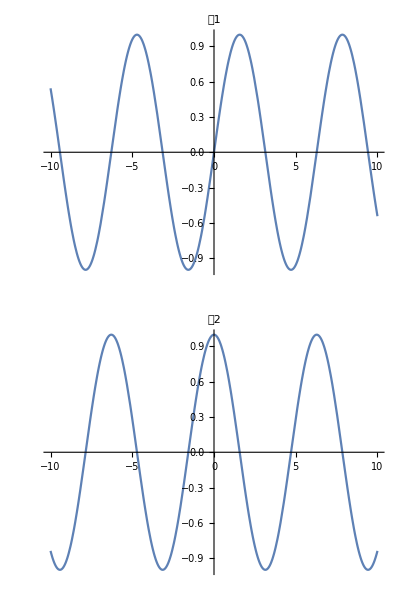

```mathematica
Plot[#,{x,-10,10},PlotLabel->#2,ImageSize->Large]&@@@{{Sin[x],"图1"},{Cos[x],"图2"}}//Column
```

#### 2. 去掉标签中数字后跟的、表示浮点精度的

若为整数或分数

```mathematica
SetPrecision[1/4,∞]
```

1/4

若为小数

```mathematica
SetPrecision[0.1,∞]
```

3602879701896397/36028797018963968

上述方式失效，改为以下代码

```mathematica
With[{r=Round[#]},r+Chop[#-r]]&@@0.1
```

0.1

#### 3. 添加PlotLegends的代码

此时，ImageSize→{478,478}

```mathematica
{{-Graphics-, -Graphics-, SetPrecision[M,∞]}, {-Graphics-, -Graphics-, SetPrecision[Ω,∞]}, {-Graphics-, -Graphics-, α}, {-Graphics-, -Graphics-, β}, {-Graphics-, -Graphics-, Subscript[ϕ, 0]}, {-Graphics-, -Graphics-, SetPrecision[n,∞]}, {-Graphics-, -Graphics-, SetPrecision[m,∞]}, {-Graphics-, -Graphics-, SetPrecision[l,∞]}, {-Graphics-, -Graphics-, SetPrecision[p,∞]}, {-Graphics-, -Graphics-, SetPrecision[Q-p,∞]}, {-Graphics-, -Graphics-, SetPrecision[P,∞]}}//Grid[#,Frame->Bottom,Background->LightBlue]&
```

-Graphics- | -Graphics- | 4
-Graphics- | -Graphics- | 1/4
-Graphics- | -Graphics- | π/2
-Graphics- | -Graphics- | π/2
-Graphics- | -Graphics- | π/2
-Graphics- | -Graphics- | 15
-Graphics- | -Graphics- | 30
-Graphics- | -Graphics- | 1
-Graphics- | -Graphics- | -1
-Graphics- | -Graphics- | 5
-Graphics- | -Graphics- | 1

#### 4. 用FrameLabel添加“态”

```mathematica
FrameLabel->-Graphics-
```

#### 5. 用PlotLabel说明绘制的是相位图还是光强图

```mathematica
PlotLabel->-Graphics-
```

#### 6. 相应的MaTeX代码

```mathematica
MaTeX["\\left|\\Psi_{n, m, l}^{M, P,p,q}\\right\\rangle",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\mathcal{P}_{n+p K, m+(Q-p), l-P K}^{M, \\Omega, \\alpha,\\beta,\\phi_{0}}(x,y,0)",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\mathcal{I}_{n+p K, m+(Q-p), l-P K}^{M, \\Omega, \\alpha,\\beta,\\phi_{0}}(x,y,0)",Magnification->2]
```

-Graphics-

#### 7. 效果

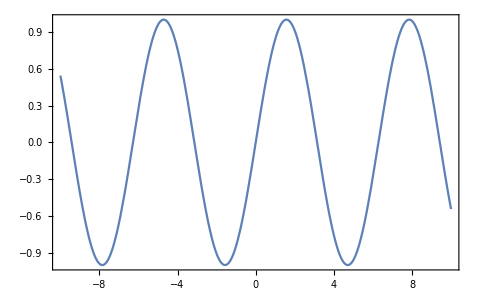
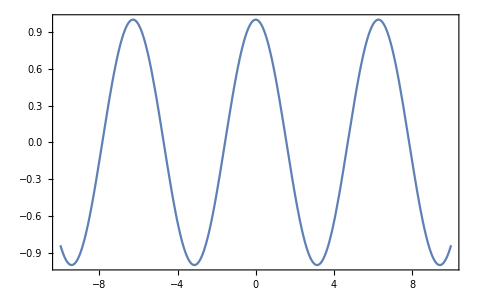

```mathematica
Plot[#,{x,-10,10},Background->White,ImageSize->{478,478},PlotLegends->#2,PlotLabel->#3,Frame->True,FrameLabel->#4]&@@@{{Sin[x],,-Graphics-,-Graphics-},{Cos[x],,-Graphics-,-Graphics-}}//Column//Print
```

```mathematica
DensityPlot[#,{x,-3,3},{y,-3,3},PlotRange->All,Exclusions->None,Background->White,ColorFunction->GrayLevel,PlotPoints->100,ImageSize->{478,478},PlotLegends->#2,PlotLabel->#3,Frame->True,FrameLabel->#4]&@@@{{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,α,β,Subscript[ϕ, 0],M],,-Graphics-,-Graphics-},{(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,α,β,Subscript[ϕ, 0],M],,-Graphics-,-Graphics-}}//Column//CloudDeploy
```

# SU(2)相干光的含义

仅当相干叠加时，才可能成为SU(2)相干光

If photons are “coherent”, they do oscillate “in phase0” with each other.

决定是否相干的关键参数是M，M越大，相干叠加的次数越多，M=0时为退相干。

## 1. 退相干

## 2. 相干

## 转换为柱坐标系后的作图问题

```mathematica
(*令-Graphics-，以便于计算*)
c=π;
(*-Graphics-,令-Graphics-计算-Graphics-*)
L=1.;
(*输入波长，单位um*)
λ=0.532;
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=N[Numerator[Rationalize@Ω]];
Q=N[Denominator[Rationalize@Ω]];
(*计算腔径,需首先清楚R的赋值*)
R=.
R=NSolve[L/R==(Sin[Ω*π])^2,R]⟦1,1⟧/.Rule->Set;
(*输入固有横模指数n*)
n=15.;
(*输入整数p*)
p=-1.;
(*输入固有横模指数m*)
m=30.;
(*输入固有纵模指数l*)
l=1.;
M=4.;
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,s_] ⟺ 2π Subscript[f, n_,m_,s_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
Notation[Subscript[d, n_,m_]^k_[β_] ⟺ WignerD[{(n_+m_)/2,k_-(n_+m_)/2,(n_-m_)/2},β_]]
Notation[Subscript[Φ, n_,m_]^(HG)[x_,y_,z_] ⟺ 1/(√(2^(m_+n_-1)π m_!n_!))1/w[z_] Subscript[H, n_][(√2 x_)/w[z_]]Subscript[H, m_][(√2 y_)/w[z_]]Exp[-(x_^2+y_^2)/(w[z_])^2]]
Notation[Subscript[ψ, n_,m_,l_]^(HG)[x_,y_,z_] ⟺ √(2/L)Subscript[Φ, n_,m_]^(HG)[x_,y_,z_]Exp[ⅈ*Subscript[k, n_,m_,l_]*z̃[x_,y_,z_]-ⅈ(m_+n_+1)ϑ[z_]]]
Notation[Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_] ⟺ Exp[ⅈ(n_+m_)/2 α_]∑_(k=0)^(n_+m_) Exp[ⅈ*k*α_]*Subscript[d, n_,m_]^k[β_]Subscript[ψ, k,n_+m_-k,l_]^(HG)[x_,y_,z_]]
Notation[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ 1/2^(M_/2)∑_(K=0)^M_ Sqrt[M_!/(K!(M_-K)!)]Exp[ⅈ*K*γ_]*Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Arg[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]*(Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_])*//Norm]
```

```mathematica
n=2
m=1
DensityPlot[#,{x,-3,3},{y,-3,3},PlotRange->All,Exclusions->None,ColorFunction->GrayLevel,PlotPoints->50,ImageSize->Medium]&/@{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,π,π 3/2,π,0],(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,π,π 3/2,π,0]}//Rasterize[#,RasterSize->500]&
```

2

1

-Graphics-

方案，先用极坐标进行推导，最后在转换到直角坐标中用DensityPlot绘图

举例

```mathematica
f[x_,y_]:=x^2+y^2
DensityPlot[f[x,y],{x,-10,10},{y,-10,10}]//Rasterize[#,RasterSize->400]&
DensityPlot[f[r Cos[θ],r Sin[θ]]/.{r->√(x^2+y^2),θ->ArcTan[x,y]},{x,-10,10},{y,-10,10}]//Rasterize[#,RasterSize->400]&
```

-Graphics-

-Graphics-

实战

```mathematica
DensityPlot[#,{x,-3,3},{y,-3,3},PlotRange->All,Exclusions->None,ColorFunction->GrayLevel,PlotPoints->50,ImageSize->Medium]&/@{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[r Cos[θ],r Sin[θ],0,π/2,π/2,π/2,M]/.{r->√(x^2+y^2),θ->ArcTan[x,y]},(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[r Cos[θ],r Sin[θ],0,π/2,π/2,π/2,M]/.{r->√(x^2+y^2),θ->ArcTan[x,y]}}//Rasterize[#,RasterSize->500]&//AbsoluteTiming
```

{20.2787,-Graphics-}

## SU(2)紧聚焦

### 3. 2. 近轴光场的聚焦

聚焦场由①聚焦镜的边界条件；②入射场决定。

-Graphics-
激光通过消球差镜聚焦

#### 理论推导

透镜附近的场：几何光学表示，此时，；能量沿光线传输；平均能量密度以沿垂直于几何波前方向传播。

消色差镜遵循：正弦条件；强度定律

-Graphics-
正弦条件：消色差镜上折射由半径为的球面决定

-Graphics-
强度定律：光线携带的能量守恒

为方便计算参考球面上的折射，将入射矢分解为。

n_ϕ不变；n_ρ→n_θ￿。故总折射场：E_∞

E_∞=={t^s(E_inc·n_ϕ)n_ϕ+t^p(E_inc·n_ρ)n_θ}√(n_1/n_2)(cosθ)^(1/2)

n_ρ | ==cosϕ n_x+sinϕ n_y 
 n_ϕ  |  ==-sinϕ n_x+cosϕ n_y 
 n_θ  |  ==cosθcosϕ n_x+cosθsinϕ n_y-sinθ n_z

得聚焦右侧镜参考球面上的场为

-Graphics-

聚焦场表达式（角谱表达式）

-Graphics-

将上式中k_x,k_y换掉

k_x==ksinθcosϕ
k_y==ksinθsinϕ
k_z==kcosθ

并将(x,y)换掉

x==ρcosφ
y==ρsinφ

将k_x,k_y上的平面积分换为(θ,ϕ)上的球面积分

-Graphics-

则将聚焦场的角谱式表示为

-Graphics-

#### 总结

下面两式计算任意光场Einc的通过焦距f和数值孔径NA的消色差镜的聚焦场

-Graphics-

### 3.6 聚焦场（近轴近似）

一般，物镜后孔径直径只有几毫米，为充分利用NA，入射光需覆盖物镜。因为入射光很宽，故用近轴近似。设沿入射光为方向的完全偏振光

近轴近似: Sin[θ]=Tan[θ]≈θ；Cos[θ]≈1

设入射光的束腰与物镜匹配，以平面波前照射在物镜上。假设物镜上渡有良好的减反射层⟹忽略菲尼尔透射系数

则，表示为

-Graphics-

需确定入射光的振幅分布，3种低阶HG模

以(0,0)模式的推导为例

```mathematica
θ=.;
ϕ=.;
(Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[f Sin[θ]Cos[ϕ],f Sin[θ]Sin[ϕ],f Cos[θ],π/2,π/2,π/2,4]
```

```mathematica
θ=.;
ϕ=.;
(Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[f Sin[θ]Cos[ϕ],f Sin[θ]Sin[ϕ],z,π/2,π/2,π/2,4]//FullSimplify
```

$Aborted

```mathematica
(Subscript[Ψ, n_,m_,l_]^(SU(2)))[f Sin[θ_]Cos[ϕ_],f Sin[θ_]Sin[ϕ_],f Cos[θ_],α_,β_,γ_,M_]
```

```mathematica
Notation[Subscript[Ε, n_,m_,l_]^∞[θ_,ϕ_,α_,β_,γ_,M_] ⟺ 1/2 Subscript[Ψ, n_,m_,l_]^(SU(2))[f Sin[θ_]Cos[ϕ_],f Sin[θ_]Sin[ϕ_],f Cos[θ_],α_,β_,γ_,M_]({{(1+Cos[θ_])-(1-Cos[θ_])Cos[2ϕ_]}, {-(1-Cos[θ_])Sin[2ϕ_]}, {-2Cos[ϕ_]Sin[θ_]}})√(Cos[θ_] Subscript[n, 1]/Subscript[n, 2])]
Notation[Subscript[𝒫, n_,m_,l_]^∞[θ_,ϕ_,α_,β_,γ_,M_] ⟺ Arg[Subscript[Ε, n_,m_,l_]^∞[θ_,ϕ_,α_,β_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^∞[θ_,ϕ_,α_,β_,γ_,M_] ⟺ Subscript[Ε, n_,m_,l_]^∞[θ_,ϕ_,α_,β_,γ_,M_]*(Subscript[Ε, n_,m_,l_]^∞[θ_,ϕ_,α_,β_,γ_,M_])*]
(Subscript[Ε, n+p*K,m+(Q-p)K,l-P*K]^∞)[1,1,π/2,π/2,π/2,4]
(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^∞)[1,1,π/2,π/2,π/2,4]
(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^∞)[1,1,π/2,π/2,π/2,4]
```

{{0.00148576+0.00109576 ⅈ},{-0.000358655-0.000264511 ⅈ},{-0.000780198-0.000575402 ⅈ}}

{{0.635458},{-2.50613},{-2.50613}}

{{3.40815×10^-6+0. ⅈ},{1.98599×10^-7+0. ⅈ},{9.39796×10^-7+0. ⅈ}}

绘制光强

```mathematica
DensityPlot[(Subscript[Ε, n+p*K,m+(Q-p)K,l-P*K]^∞)[θ,ϕ,π/2,π/2,π/2,4]//Norm,{θ,0,Subscript[θ, max]},{ϕ,0,2π}]
DensityPlot[(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^∞)[θ,ϕ,π/2,π/2,π/2,4]//Norm,{θ,0,Subscript[θ, max]},{ϕ,0,2π},ColorFunction->GrayLevel]
DensityPlot[(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^∞)[θ,ϕ,π/2,π/2,π/2,4]//Norm,{θ,0,Subscript[θ, max]},{ϕ,0,2π},ColorFunction->GrayLevel]
```

```mathematica
θ=.
ϕ=.
Notation[Subscript[Ε, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,θ_,ϕ_,α_,β_,γ_,M_] ⟺ (ⅈ k f ⅇ^(-ⅈ k f))/(2π)Integrate[Subscript[Ε, n_,m_,l_]^∞[θ_,ϕ_,α_,β_,γ_,M_] ⅇ^(ⅈ k z_ Cos[θ_])ⅇ^(ⅈ k ρ_ Sin[θ_]Cos[ϕ_-φ_])Sin[θ_],{ϕ,θ}]]
```

```mathematica
(Subscript[Ε, n,m,l]^(SU(2)))[ρ,φ,z,θ,ϕ,α,β,γ,M]
```

Integrate::ilim: Invalid integration variable or limit(s) in {ϕ,θ}.

(-6.27019×10^-12+160. ⅈ) Integrate[{{0.101455 ⅇ^((1) z Cos[θ]+1) √Cos[θ] (1+Cos[θ]-(1-Cos[θ]) Cos[2 ϕ]) Sin[θ] (1)},{0.101455 5 (1)},{1}},{ϕ,θ}]
 |  |  |  |

```mathematica
x=.
y=.
```

```mathematica
Integrate[Integrate[x^2+Sin[x],x],y]
```

(x^3 y)/3-y Cos[x]

```mathematica
{n+p*K,m+(Q-p)K,l-P*K}
```

{15.-1. K,30.+5. K,1.-1. K}

```mathematica
Integrate[Integrate[(Subscript[Ε, n+p*K,m+(Q-p)K,l-P*K]^∞)[θ,ϕ,π/2,π/2,π/2,4] ⅇ^(ⅈ k z Cos[θ])ⅇ^(ⅈ k ρ Sin[θ]Cos[ϕ-φ])Sin[θ],ϕ],θ]
```

$Aborted

```mathematica
Integrate[(Subscript[Ε, n,m,l]^∞)[θ,ϕ,α_,β_,γ_,M_] ⅇ^(ⅈ k z_ Cos[θ])ⅇ^(ⅈ k ρ_ Sin[θ]Cos[ϕ-φ_])Sin[θ],{ϕ,0,2π},{θ,0,Subscript[θ, max]}]
```

为了便于算出结果，上面的定义中保留最少的变量

```mathematica
θ=.
ϕ=.
Notation[Subscript[Ε, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_] ⟺ (ⅈ k f ⅇ^(-ⅈ k f))/(2π)NIntegrate[Subscript[Ε, n_,m_,l_]^∞[θ,ϕ,α_,β_,γ_,M_] ⅇ^(ⅈ k z_ Cos[θ])ⅇ^(ⅈ k ρ_ Sin[θ]Cos[ϕ-φ_])Sin[θ],{ϕ,0,2π},{θ,0,Subscript[θ, max]}]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_] ⟺ Arg[Subscript[Ε, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_] ⟺ Subscript[Ε, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_]*(Subscript[Ε, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_])*]
(Subscript[Ε, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[1,π,0,π/2,π/2,π/2,4]//Norm
(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[1,π,0,π/2,π/2,π/2,4]//Norm
(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[1,π,0,π/2,π/2,π/2,4]//Norm
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.39537×10^-7+9.21726×10^-6 ⅈ and 0.000331563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.54579×10^-8-9.3739×10^-7 ⅈ and 0.0000400429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

方式2，不必要的量不要出现

```mathematica
{n+p*K,m+(Q-p)K,l-P*K}
```

{15.-1. K,30.+5. K,1.-1. K}

```mathematica
θ=1;
ϕ=1;
(Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[f Sin[θ]Cos[ϕ],f Sin[θ]Sin[ϕ],f Cos[θ],π/2,π/2,π/2,4]
```

0.00287638+0.00212135 ⅈ

```mathematica
(Subscript[Ψ, n_,m_,l_]^(SU(2)))[f Sin[θ_]Cos[ϕ_],f Sin[θ_]Sin[ϕ_],f Cos[θ_],α_,β_,γ_,M_]
```

```mathematica
Notation[Ε^∞[θ_,ϕ_] ⟺ 1/2 Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Sin[θ_]Cos[ϕ_],f Sin[θ_]Sin[ϕ_],f Cos[θ_],π/2,π/2,π/2,4]({{(1+Cos[θ_])-(1-Cos[θ_])Cos[2ϕ_]}, {-(1-Cos[θ_])Sin[2ϕ_]}, {-2Cos[ϕ_]Sin[θ_]}})√(Cos[θ_] Subscript[n, 1]/Subscript[n, 2])]
Notation[𝒫^∞[θ_,ϕ_] ⟺ Arg[Ε^∞[θ_,ϕ_]]]
Notation[𝕀^∞[θ_,ϕ_] ⟺ Ε^∞[θ_,ϕ_]*(Ε^∞[θ_,ϕ_])*]
(Ε^∞)[1,1]
(𝒫^∞)[1,1]
(𝕀^∞)[1,1]
```

{{0.00148576+0.00109576 ⅈ},{-0.000358655-0.000264511 ⅈ},{-0.000780198-0.000575402 ⅈ}}

{{0.635458},{-2.50613},{-2.50613}}

{{3.40815×10^-6+0. ⅈ},{1.98599×10^-7+0. ⅈ},{9.39796×10^-7+0. ⅈ}}

绘制光强

```mathematica
DensityPlot[(Subscript[Ε, n+p*K,m+(Q-p)K,l-P*K]^∞)[θ,ϕ,π/2,π/2,π/2,4]//Norm,{θ,0,Subscript[θ, max]},{ϕ,0,2π}]
DensityPlot[(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^∞)[θ,ϕ,π/2,π/2,π/2,4]//Norm,{θ,0,Subscript[θ, max]},{ϕ,0,2π},ColorFunction->GrayLevel]
DensityPlot[(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^∞)[θ,ϕ,π/2,π/2,π/2,4]//Norm,{θ,0,Subscript[θ, max]},{ϕ,0,2π},ColorFunction->GrayLevel]
```

```mathematica
θ=.
ϕ=.
Notation[Ε^(SU(2))[ρ_,φ_,z_] ⟺ (ⅈ k f ⅇ^(-ⅈ k f))/(2π)Integrate[Ε^∞[θ,ϕ] ⅇ^(ⅈ k z_ Cos[θ])ⅇ^(ⅈ k ρ_ Sin[θ]Cos[ϕ-φ_])Sin[θ],{ϕ,0,2π},{θ,0,Subscript[θ, max]}]]

(Ε^(SU(2)))[1,1,1]
```

$Aborted

```mathematica
(Ε^∞)[θ,ϕ]//FullSimplify
```

$Aborted

```mathematica
θ=.
ϕ=.

EE[ρ_,φ_,z_]:=(ⅈ k f ⅇ^(-ⅈ k f))/(2π)NIntegrate[(Ε^∞)[θ,ϕ] ⅇ^(ⅈ k z Cos[θ])ⅇ^(ⅈ k ρ Sin[θ]Cos[ϕ-φ])Sin[θ],{ϕ,0,2π},{θ,0,Subscript[θ, max]},WorkingPrecision->100]
EE[0,0,0]
(*Table[EE[ρ,φ,0],{ρ,{-1,0,1}},{φ,{0,π}}]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

为了便于算出结果，上面的定义中保留最少的变量

```mathematica
θ=.
ϕ=.
Notation[Subscript[Ε, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_] ⟺ (ⅈ k f ⅇ^(-ⅈ k f))/(2π)NIntegrate[Subscript[Ε, n_,m_,l_]^∞[θ,ϕ,α_,β_,γ_,M_] ⅇ^(ⅈ k z_ Cos[θ])ⅇ^(ⅈ k ρ_ Sin[θ]Cos[ϕ-φ_])Sin[θ],{ϕ,0,2π},{θ,0,Subscript[θ, max]}]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_] ⟺ Arg[Subscript[Ε, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_] ⟺ Subscript[Ε, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_]*(Subscript[Ε, n_,m_,l_]^(SU(2))[ρ_,φ_,z_,α_,β_,γ_,M_])*]
(Subscript[Ε, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[1,π,0,π/2,π/2,π/2,4]//Norm
(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[1,π,0,π/2,π/2,π/2,4]//Norm
(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[1,π,0,π/2,π/2,π/2,4]//Norm
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.39537×10^-7+9.21726×10^-6 ⅈ and 0.000331563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

10和01模由下式产生

-Graphics-

用球坐标系表示该坐标

-Graphics-

则

-Graphics-

因子适用于所有模式

f_w(θ)==exp(-f^2 sin^2 θ/w_0^2)

聚焦场依赖于①多少入射光关于透镜尺寸被展开【衍射是傅里叶变换】。透镜的孔径=fsin θ_max，假设填充因子

束腰/透镜半径

f_0==w_0/(fsin θ_max)

在模式振幅写入指数方程【变迹方程/看做光阑】

f_w(θ)==e^(-1/f_0^2(sin^2 θ)/(sin^2 θ_max))

焦点处的聚焦场，用下面的恒等式

∫_0^(2π) cosnϕ e^(ixcos(ϕ-φ))dϕ==2π(i^n)J_n(x)cosnφ
∫_0^(2π) sinnϕ e^(ixcos(ϕ-φ))dϕ==2π(i^n)J_n(x)sinnφ

关于ϕ积分，聚焦场的最终表达式只含θ。

-Graphics-

-Graphics-

注：I_ij==I_ij(ρ,z)，故数值计算每点处的积分。故聚焦场的表达式为

-Graphics-

-Graphics-

-Graphics-

## 代码

#### 绘制

注：入射光场=Ψ_(n+p*K,m+(Q-p)K,l-P*K)^(SU(2))[f Sin[θ]Cos[ϕ],f Sin[θ]Sin[ϕ],f,π/2,π/2,π/2,4]；总折射光场

```mathematica
Subscript[n, 1]=1.;
Subscript[n, 2]=1.518;
NA=1.3;
Subscript[θ, max]=.
Subscript[θ, max]=Solve[NA==Subscript[n, 2]*Sin[Subscript[θ, max]],Subscript[θ, max],InverseFunctions->True]⟦1,1⟧/.Rule->Set;

f=0.16*1000;(*100倍物镜的焦距一般为0.13~0.19mm*)
k=2.π;
Subscript[Ε, 0]=100.;(*估计功率为100mW*)
```

理论部分

用正弦条件，光学系统如下所示

-Graphics-

说明：由于光束关于z轴对称，故

且没有

故，应该有这样的关系

-Graphics-

球面上的任意点为(x_∞,y_∞,z_∞)/(f,θ,ϕ)
焦点附近的场点为(x,y,z)/(r,ϑ,φ)

为描述参考面上的折射，引入柱坐标系的单位矢量n_ρ  n_ϕ，球坐标系的单位矢量n_θ  n_ϕ

注：
柱系的光束为入射光
球系为聚焦光

计算参考球上的折射

将入射光分为两个分量：OverVector[Ε_int^(s)] OverVector[Ε_int^(p)] ，则将两个场分量表示为

OverVector[Ε_int^(s)]=(OverVector[Ε_int]·OverVector[n_ϕ])OverVector[n_ϕ]
OverVector[Ε_int^(p)]=(OverVector[Ε_int]·OverVector[n_ρ])OverVector[n_ρ]

说明：s偏振垂直纸面，故是入射光OverVector[Ε_int]关于柱坐标单位矢量OverVector[n_ϕ]的分量；p偏振平行纸面，故是入射光OverVector[Ε_int]关于柱坐标单位矢量OverVector[n_ρ]的分量

s和p两分量，经球面折射后，由柱坐标系进入球坐标系，该过程中，单位矢量OverVector[n_ϕ]保持不变，而单位矢量OverVector[n_ρ]变为OverVector[n_θ]，则总折射场

如何理解单位矢量OverVector[n_ρ]变为OverVector[n_θ]？

答：分量不变，仍为OverVector[Ε_int]·OverVector[n_ρ]，只是单位矢量OverVector[n_ρ]变为OverVector[n_θ]，故

为方便推导，令t^s=t^p=1

OverVector[Ε_∞]=[(OverVector[Ε_int]·OverVector[n_ϕ])OverVector[n_ϕ]+(OverVector[Ε_int]·OverVector[n_ρ])OverVector[n_θ]]√(n_1/n_2)Cos[θ]

下标∞表明场在距离焦点(x,y,z)==(0,0,0)很远处计算。

用笛卡尔坐标系中的单位矢n_x,n_y,n_z表示球、柱坐标系中的单位矢n_ρ,n_θ,n_ϕ，其中θ和ϕ为球系坐标

OverVector[n_ρ]=Cos[ϕ]OverVector[n_x]+Sin[ϕ]OverVector[n_y]
OverVector[n_ϕ]=-Sin[ϕ]OverVector[n_x]+Cos[ϕ]OverVector[n_y]
OverVector[n_θ]=Cos[θ]Cos[ϕ]OverVector[n_x]+Cos[θ]Sin[ϕ]OverVector[n_y]-Sin[θ]OverVector[n_z]

```mathematica
OverVector[Subscript[n, ρ]]=({{Cos[ϕ]}, {Sin[ϕ]}, {0}});
OverVector[Subscript[n, ϕ]]=({{-Sin[ϕ]}, {Cos[ϕ]}, {0}});
OverVector[Subscript[n, θ]]=({{Cos[θ]Cos[ϕ]}, {Cos[θ]Sin[ϕ]}, {-Sin[θ]}});
OverVector[Subscript[n, ϕ]]*OverVector[Subscript[n, ϕ]]//MatrixForm
OverVector[Subscript[n, ρ]]*OverVector[Subscript[n, θ]]//MatrixForm
OverVector[Subscript[Ε, ∞]]=(OverVector[Subscript[Ε, int]]*OverVector[Subscript[n, ϕ]]*OverVector[Subscript[n, ϕ]]+OverVector[Subscript[Ε, int]]*OverVector[Subscript[n, ρ]]*OverVector[Subscript[n, θ]])√(Subscript[n, 1]/Subscript[n, 2])√Cos[θ]//MatrixForm
```

(Sin[ϕ]^2
Cos[ϕ]^2
0)

(Cos[θ] Cos[ϕ]^2
Cos[θ] Sin[ϕ]^2
0)

(0.811641 √Cos[θ] (OverVector[Ε_int] Cos[θ] Cos[ϕ]^2+OverVector[Ε_int] Sin[ϕ]^2)
0.811641 √Cos[θ] (OverVector[Ε_int] Cos[ϕ]^2+OverVector[Ε_int] Cos[θ] Sin[ϕ]^2)
0.)

即，聚焦镜的参考球右侧，笛卡尔坐标系中的场的表达式。

将场点【而非参考求上】横模坐标分量表示为(x,y)

x=ρ cos(φ)
y=ρ sin(φ)

简单暴力地将直角坐标分量转换为球坐标分量

坐标变换

```mathematica
CoordinateTransformData["Spherical"->"Cartesian","Mapping", {r,θ,φ}]
```

{r Cos[φ] Sin[θ],r Sin[θ] Sin[φ],r Cos[θ]}

```mathematica
(Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[f Cos[ϕ] Sin[θ],f Sin[θ] Sin[ϕ],-f Cos[θ],π/2,π/2,π/2,4]//AbsoluteTiming
```

```mathematica
Notation[Subscript[Ε, ∞][ρ_,θ_,ϕ_] ⟺ 1/2 Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[ρ_ Cos[ϕ_] Sin[θ_],ρ_ Sin[θ_] Sin[ϕ_],-ρ_ Cos[θ_],π/2,π/2,π/2,4]({{(1+Cos[θ_])-(1-Cos[θ_])Cos[2ϕ_]}, {-(1-Cos[θ_])Sin[2ϕ_]}, {-2Cos[ϕ_]Sin[θ_]}})√(Cos[θ_] Subscript[n, 1]/Subscript[n, 2])]
(*定义相位*)
Notation[Subscript[𝒫, ∞][ρ_,θ_,ϕ_] ⟺ Arg[Subscript[Ε, ∞][ρ_,θ_,ϕ_]]]
(*定义光强*)
Notation[Subscript[𝕀, ∞][ρ_,θ_,ϕ_] ⟺ Subscript[Ε, ∞][ρ_,θ_,ϕ_]*(Subscript[Ε, ∞][ρ_,θ_,ϕ_])*]
(*计算振幅及其各分量验证振幅定义是否正确*)
Subscript[Ε, ∞][f,Subscript[θ, max],2π]//Norm
Subscript[Ε, ∞][f,Subscript[θ, max],2π]⟦1⟧
Subscript[Ε, ∞][Subscript[θ, max],2π]⟦2⟧
Subscript[Ε, ∞][Subscript[θ, max],2π]⟦3⟧
(*计算振幅及其各分量验证相位定义是否正确*)
Subscript[𝒫, ∞][f,Subscript[θ, max],2π]//Norm
Subscript[𝒫, ∞][f,Subscript[θ, max],2π]⟦1⟧
Subscript[𝒫, ∞][f,Subscript[θ, max],2π]⟦2⟧
Subscript[𝒫, ∞][f,Subscript[θ, max],2π]⟦3⟧
(*计算振幅及其各分量验证光强定义是否正确*)
Subscript[𝕀, ∞][f,Subscript[θ, max],2π]//Norm
Subscript[𝕀, ∞][f,Subscript[θ, max],2π]⟦1⟧
Subscript[𝕀, ∞][f,Subscript[θ, max],2π]⟦2⟧
Subscript[𝕀, ∞][f,Subscript[θ, max],2π]⟦3⟧
```

0.00255822

{0.00102252-0.000836182 ⅈ}

{0.+0. ⅈ}

{-0.00169596+0.0013869 ⅈ}

2.54997

{-0.685482}

{0.}

{2.45611}

5.10704×10^-6

{1.74474×10^-6+0. ⅈ}

{0.+0. ⅈ}

{4.79976×10^-6+0. ⅈ}

转换为直角坐标系

```mathematica
Subscript[Ε, ∞][ρ,θ,ϕ]/.{ρ->√(x^2+y^2+z^2),θ->ArcTan[z,√(x^2+y^2)],ϕ->ArcTan[x,y]}
```

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

{{Indeterminate},{Indeterminate},{Indeterminate}}

```mathematica
Table[Subscript[𝕀, ∞][ρ,θ,ϕ]/.{ρ->√(x^2+y^2+z^2),θ->ArcTan[z,√(x^2+y^2)],ϕ->ArcTan[x,y]}//Norm,{}]
```

```mathematica
z=f;
DensityPlot[Subscript[𝕀, ∞][ρ,θ,ϕ]/.{ρ->√(x^2+y^2+z^2),θ->ArcTan[z,√(x^2+y^2)],ϕ->ArcTan[x,y]}//Norm,{x,-3,3},{y,-3,3}]
```

$Aborted

```mathematica
x=0;
y=0;
z=f;
Subscript[𝕀, ∞][ρ,θ,ϕ]/.{ρ->√(x^2+y^2+z^2),θ->ArcTan[z,√(x^2+y^2)],ϕ->ArcTan[x,y]}//Norm
```

160.

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

Norm::mindet: Input matrix contains an indeterminate entry.

Norm[{{Indeterminate},{Indeterminate},{Indeterminate}}]

```mathematica
ToSphericalCoordinates[{x,y,z}]
```

Thread::tdlen: Objects of unequal length in {√(x^2+y^2+z^2),ArcTan[z,√(x^2+y^2)],ArcTan[x,y]} {θ→ArcTan[z,√(x^2+y^2)],ϕ→ArcTan[x,y]} cannot be combined.

{θ→ArcTan[z,√(x^2+y^2)],ϕ→ArcTan[x,y]} {√(x^2+y^2+z^2),ArcTan[z,√(x^2+y^2)],ArcTan[x,y]}

```mathematica
√(x^2+y^2+z^2)==f
```

```mathematica
z=.;f=.;Solve[√(x^2+y^2+z^2)==f,z]
```

```mathematica
{{z->-√(f^2-x^2-y^2)},{z->√(f^2-x^2-y^2)}}
```

绘图

```mathematica
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
```

```mathematica
DensityPlot[Subscript[Ε, ∞][θ,ϕ]//Norm,{θ,0.,3},{ϕ,0.,2.π},ColorFunction->GrayLevel,PlotPoints->100]
(*DensityPlot[Subscript[𝒫, ∞][θ,ϕ]//Norm,{θ,0.,Subscript[θ, max]},{ϕ,0.,2.π},ColorFunction->GrayLevel]
DensityPlot[Subscript[𝕀, ∞][θ,ϕ]//Norm,{θ,0.,Subscript[θ, max]},{ϕ,0.,2.π},ColorFunction->GrayLevel]*)
```

计算积分

```mathematica
NIntegrate[Subscript[Ε, ∞][θ,ϕ],{θ,0,Subscript[θ, max]},{ϕ,0,2π},PrecisionGoal->100,WorkingPrecision->200]
```

$Aborted

```mathematica
NIntegrate[Subscript[Ε, ∞][θ,ϕ],{θ,0,Subscript[θ, max]}]
```

```mathematica
Subscript[Ε, ∞][Subscript[θ, max],#]&/@Range[0,2π,0.1π]//MatrixForm
```

((0.0000579037+0.000851392 ⅈ) | (0.+0. ⅈ) | (-0.0000960398-0.00141213 ⅈ)
(-0.0000693831-0.000533359 ⅈ) | (0.000017533+0.000134779 ⅈ) | (0.000100461+0.000772259 ⅈ)
(-0.000597657+0.00123508 ⅈ) | (0.000201132-0.000415646 ⅈ) | (0.000605878-0.00125207 ⅈ)
(0.000932236+0.00141097 ⅈ) | (-0.000257431-0.000389629 ⅈ) | (-0.000563411-0.000852739 ⅈ)
(0.0000546612-0.000917543 ⅈ) | (-8.14618×10^-6+0.000136742 ⅈ) | (-0.0000151659+0.000254576 ⅈ)
(0.0000754185+0.00161446 ⅈ) | (-2.23361×10^-21-4.78142×10^-20 ⅈ) | (-3.95485×10^-21-8.46601×10^-20 ⅈ)
(0.00200654+0.000621011 ⅈ) | (0.000299035+0.0000925495 ⅈ) | (0.000556722+0.000172302 ⅈ)
(0.000155777-0.000992073 ⅈ) | (0.0000430169-0.000273955 ⅈ) | (0.0000941463-0.000599574 ⅈ)
(0.000192933+0.000780263 ⅈ) | (0.0000649285+0.000262585 ⅈ) | (0.000195586+0.000790995 ⅈ)
(0.00111594-0.000529221 ⅈ) | (0.000281996-0.000133734 ⅈ) | (0.00161578-0.000766267 ⅈ)
(-0.0000579037-0.000851392 ⅈ) | (-6.64263×10^-21-9.76704×10^-20 ⅈ) | (-0.0000960398-0.00141213 ⅈ)
(0.0000693831+0.000533359 ⅈ) | (-0.000017533-0.000134779 ⅈ) | (0.000100461+0.000772259 ⅈ)
(0.000597657-0.00123508 ⅈ) | (-0.000201132+0.000415646 ⅈ) | (0.000605878-0.00125207 ⅈ)
(-0.000932236-0.00141097 ⅈ) | (0.000257431+0.000389629 ⅈ) | (-0.000563411-0.000852739 ⅈ)
(-0.0000546612+0.000917543 ⅈ) | (8.14618×10^-6-0.000136742 ⅈ) | (-0.0000151659+0.000254576 ⅈ)
(-0.0000754185-0.00161446 ⅈ) | (6.70084×10^-21+1.43443×10^-19 ⅈ) | (-1.18646×10^-20-2.5398×10^-19 ⅈ)
(-0.00200654-0.000621011 ⅈ) | (-0.000299035-0.0000925495 ⅈ) | (0.000556722+0.000172302 ⅈ)
(-0.000155777+0.000992073 ⅈ) | (-0.0000430169+0.000273955 ⅈ) | (0.0000941463-0.000599574 ⅈ)
(-0.000192933-0.000780263 ⅈ) | (-0.0000649285-0.000262585 ⅈ) | (0.000195586+0.000790995 ⅈ)
(-0.00111594+0.000529221 ⅈ) | (-0.000281996+0.000133734 ⅈ) | (0.00161578-0.000766267 ⅈ)
(0.0000579037+0.000851392 ⅈ) | (1.32853×10^-20+1.95341×10^-19 ⅈ) | (-0.0000960398-0.00141213 ⅈ))

```mathematica
Integrate[Subscript[Ε, ∞][θ,ϕ],{θ,0,Subscript[θ, max]},{ϕ,0,2π}]
```

$Aborted

尝试用分量算一下积分

```mathematica
n=15;Notation[Subscript[Ε, ∞][θ_,ϕ_] ⟺ 1/2 Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Cos[ϕ_],f*Sin[ϕ_],f,π/2,π/2,π/2,4]((1+Cos[θ_])-(1-Cos[θ_])Cos[2ϕ_])√(Cos[θ_] Subscript[n, 1]/Subscript[n, 2])]
Subscript[Ε, ∞][Subscript[θ, max],π]
DensityPlot[Subscript[Ε, ∞][θ,ϕ]//Norm,{θ,0.,Subscript[θ, max]},{ϕ,0.,2.π},ColorFunction->GrayLevel]

(*Integrate[Subscript[Ε, ∞][θ,ϕ],{θ,0,Subscript[θ, max]},{ϕ,0,2π}]*)
```

1/4 (1) Cos[θ_max] √((n_1 Cos[θ_max])/n_2)
 |  |  |  |

DensityPlot::plln: Limiting value θ_max in {θ,0.,θ_max} is not a machine-sized real number.

DensityPlot[Norm[1/(2 2^(4/2))(∑_(K=0)^4 √((4!)/(K! (4-K)!)) Exp[(ⅈ K π)/2] (Exp[(ⅈ ((n+p K)+(m+(Q-p) K)) π)/(2 2)] ∑_(k=0)^((n+p K)+(m+(Q-p) K)) (Exp[(ⅈ k π)/2] d_(n+p K,m+(Q-p) K)^k[π/2] (√(2/L) (H_k[(√2 (f Cos[ϕ]))/w[f]] H_((n+p K)+(m+(Q-p) K)-k)[(√2 (f Sin[ϕ]))/w[f]] Exp[-((f Cos[ϕ])^2+(f Sin[ϕ])^2)/w[f]^2]) Exp[1/c ⅈ (2 π f_((n+p K)+(m+(Q-p) K)-k,k,l-P K)) z̃[f Cos[ϕ],f Sin[ϕ],f]-ⅈ (((n+p K)+(m+(Q-p) K)-k)+k+1) ϑ[f]]))/(√(2^(((n+p K)+(m+(Q-p) K)-k)+k-1) π ((n+p K)+(m+(Q-p) K)-k)! k!) w[f]))) ((1+Cos[θ])-(1-Cos[θ]) Cos[2 ϕ]) √((Cos[θ] n_1)/n_2)],{θ,0.,θ_max},{ϕ,0.,2. π},ColorFunction→GrayLevel]

## 数值积分

```mathematica
NIntegrate[1/(√(x^1+y^2+z^3)),{x,0,1},{y,0,1},{z,0,1}]
```

1.0885

计算隐式定义的区域的面积和体积：

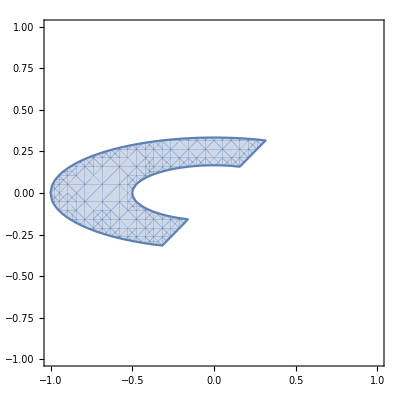

```mathematica
RegionPlot[1/4≤x^2+9 y^2≤1∧y>x,{x,-1,1},{y,-1,1}]
```

```mathematica
NIntegrate[Boole[1/4≤x^2+(3y)^2≤1∧y>x],{x,-1,1},{y,-1,1}]
```

0.392699

在任何区域上求积分：

```mathematica
ℓ=RandomReal[1,{50,3}];%//TableForm
```

0.448532 | 0.477956 | 0.268743
0.674399 | 0.290697 | 0.148041
0.173989 | 0.122094 | 0.22963
0.353956 | 0.882746 | 0.794617
0.0908187 | 0.993087 | 0.527377
0.715346 | 0.732458 | 0.0592096
0.51722 | 0.629844 | 0.785284
0.435343 | 0.523285 | 0.747685
0.295805 | 0.393344 | 0.271305
0.67954 | 0.84276 | 0.86426
0.643126 | 0.328847 | 0.102459
0.741944 | 0.535965 | 0.134644
0.468853 | 0.379121 | 0.588912
0.854674 | 0.275433 | 0.392141
0.0870689 | 0.969945 | 0.191685
0.498855 | 0.587452 | 0.141759
0.106346 | 0.771543 | 0.307232
0.415834 | 0.237769 | 0.57781
0.200736 | 0.138156 | 0.795989
0.558438 | 0.282425 | 0.351402
0.599819 | 0.99412 | 0.26874
0.700872 | 0.374001 | 0.435298
0.509831 | 0.886569 | 0.500041
0.369537 | 0.623183 | 0.707608
0.137684 | 0.677589 | 0.133638
0.484602 | 0.866335 | 0.216885
0.218116 | 0.18869 | 0.165772
0.94537 | 0.376735 | 0.119783
0.526775 | 0.001824 | 0.595477
0.937521 | 0.194512 | 0.33107
0.358218 | 0.758736 | 0.138586
0.488062 | 0.0689263 | 0.277638
0.468249 | 0.0698295 | 0.429362
0.617325 | 0.986335 | 0.401485
0.721907 | 0.521427 | 0.0599328
0.197879 | 0.630056 | 0.704916
0.381813 | 0.745462 | 0.308535
0.385892 | 0.575295 | 0.429523
0.00823665 | 0.0392531 | 0.344314
0.616219 | 0.362894 | 0.0487475
0.575997 | 0.623205 | 0.432259
0.0176595 | 0.788509 | 0.678616
0.29978 | 0.854584 | 0.25346
0.0896243 | 0.98238 | 0.483131
0.99107 | 0.570379 | 0.880501
0.166407 | 0.273549 | 0.118205
0.241415 | 0.221249 | 0.898977
0.725953 | 0.255988 | 0.730535
0.55942 | 0.863852 | 0.297483
0.606468 | 0.488739 | 0.73298

```mathematica
ℛ=ConvexHullMesh[ℓ];ℛ//Rasterize[#,RasterSize->200]&
NIntegrate[x^2+y^2 z^2,{x,y,z}∈ℛ]
∫_1^5 xⅆx
```

-Graphics-

0.247877

关于一个3D区域求积分，需要几个∫号？

```mathematica
∫_({x,y,z}∈Tetrahedron[]) (x^4 y^5+z^10)
```

∫_({x,y,z}∈Tetrahedron[]) (x^4 y^5+z^10)

求震荡及其复杂函数的积分

```mathematica
Integrate
```

```mathematica
Plot[1/x Cos[Log[x]/x],{x,0,0.01},PlotStyle->Thickness[0.0001],PlotRange->2000]//Rasterize[#,RasterSize->500]&
NIntegrate[1/x Cos[Log[x]/x],{x,0,0.01}]
```

-Graphics-

-0.00171866

### 范围

```mathematica
NIntegrate[ⅇ^(ⅇ^-x),{x,0,5}]
```

6.31115

注：∫_lower^upper exprⅆvar=Integrate；∫_lower^upper exprⅆvar//N=NIntegrate

```mathematica
∫_1^5 x^x ⅆx//N
NIntegrate[x^x,{x,1,5}]
∫_1^5 x^2 ⅆx
NIntegrate[x^2,{x,1,5}]
```

1241.03

1241.03

124/3

41.3333

无限实数范围：

```mathematica
∫_0^∞ 1/(1+x^2)ⅆx
```

π/2

```mathematica
∫_(-∞)^∞ ⅇ^(ⅈ x^2)ⅆx
```

(1+ⅈ) √(π/2)

得到高精度的结果：

```mathematica
NIntegrate[1/(1+√x),{x,0,1},PrecisionGoal->100,WorkingPrecision->200]
```

0.6137056388801093811655357570836468638489997312794894917586399810132127560606105687882733460071626249159970379588586285326289595284837388859346584967298480761385498838450271890664634918876355517462432

沿一条有限或无限长的复数直线积分：

```mathematica
NIntegrate[√x,{x,ⅈ,3-ⅈ}]
```

3.79214-2.21131 ⅈ

```mathematica
NIntegrate[Sinh[x]/x,{x,0,∞ ⅈ}]
```

-2.07802×10^-15+1.5708 ⅈ

在复平面上沿着一条分段线型等高线：

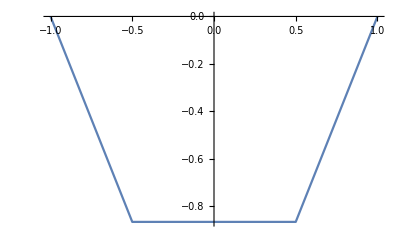

```mathematica
ListLinePlot[{{1,0},{Re@(ⅇ^((ⅈ π)/3)),Im@(ⅇ^((ⅈ π)/3))}.{Re@(ⅇ^((2 ⅈ π)/3)),Im@(ⅇ^((2 ⅈ π)/3))},{-1,0},{Re@(ⅇ^(-(2 ⅈ π)/3)),Im@(ⅇ^(-(2 ⅈ π)/3))},{Re@(ⅇ^(-(ⅈ π)/3)),Im@(ⅇ^(-(ⅈ π)/3))},{1,0}}]
```

沿折线的积分

-Graphics-

-Graphics-

```mathematica
NIntegrate[1/(z+1/2),{z,1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1,ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),1}]
```

-1.11022×10^-16+6.28319 ⅈ

```mathematica
NIntegrate[1/(z+1/2),{z,1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1,ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),∞ ⅈ,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.5+8.16907×10^224 ⅈ}. NIntegrate obtained 716.671+8.58263912306054×10^27949 ⅈ and 8.58263912306054×10^27949 for the integral and error estimates.

716.671+8.58263912306054×10^27949 ⅈ

```mathematica
NIntegrate[1/(z+1/2),{z,1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1,ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),-1/2,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-0.49999999999999999999999999997553910349376312993058392251265046735}. NIntegrate obtained 143.042+5.56946 ⅈ and 25.088 for the integral and error estimates.

143.042+5.56946 ⅈ

测试积分在中间点的奇点？

若在任意中间点x_i(x_0与x_k除外)上有奇点，则不输出结果，如无奇点，则输出从x_0⟶x_k的积分结果

复平面沿着一条环形等高线

```mathematica
NIntegrate[(ⅈ ⅇ^(ⅈ ω))/(ⅇ^(ⅈ ω)+1/2),{ω,0,2π}]
```

-1.15707×10^-12+6.28319 ⅈ

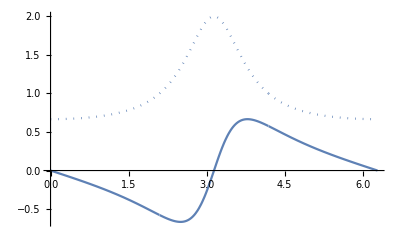

```mathematica
ReImPlot[(ⅈ ⅇ^(ⅈ ω))/(ⅇ^(ⅈ ω)+1/2),{ω,0,2π}]
```

绘制实部和积分路径

```mathematica
{Re[#],Im[#]}&/@(ⅇ^((π ⅈ)/3 Range[0,6]))
Arrow[%]
a=Graphics[%];
```

{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}}

Arrow[{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}}]

```mathematica
b=ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2π},Axes->False]/.Line->Arrow;
```

```mathematica
c=DensityPlot[Re[1/(a+1/2+ⅈ b)],{a,-1.2,1.2},{b,-1.2,1.2}];
```

```mathematica
Show[{c,a,b}]//Rasterize[#,RasterSize->300]&
```

-Graphics-

```mathematica
NIntegrate[{x,1/(√x),Sin[x]},{x,0,5}]
```

{12.5,4.47214,0.716338}

```mathematica
NIntegrate[({{x, √x, x^(1/3)}, {√x, x^(1/4), x^(1/8)}, {x^(1/9), x^0, x^(1/7)}}),{x,0,2π}]//MatrixForm
```

(19.7392 | 10.4997 | 8.69563
10.4997 | 7.9582 | 7.02748
6.936 | 6.28319 | 7.14848)

```mathematica
ReImPlot[√((x^2+1)(x^2-4)),{x,-3,3},PlotLegends->"ReIm"]//Rasterize[#,RasterSize->300]&
AbsArgPlot[√((x^2+1)(x^2-4)),{x,-3,3},PlotLegends->Automatic]//Rasterize[#,RasterSize->300]&
```

-Graphics-

-Graphics-

## 可能用到的功能

设置精度，不适用Integrate=∫_□^□ □ⅆ□，适用NIntegrate

```mathematica
NIntegrate[1/(1+Sqrt[x]),{x,0,1},PrecisionGoal->100,WorkingPrecision->200]
```

0.6137056388801093811655357570836468638489997312794894917586399810132127560606105687882733460071626249159970379588586285326289595284837388859346584967298480761385498838450271890664634918876355517462432

ReIm
AbsArg

```mathematica
ReIm[3+ⅈ]
```

{3,1}

```mathematica
Abs[5+13ⅈ]
AbsArg[5+13ⅈ]
```

√194

{√194,ArcTan[13/5]}

ReImPlot实虚部图
AbsArgPlot幅角着色的绝对值图

#### 多元函数

```mathematica
NIntegrate[BesselJ[3,y]/(x+1),{x,0,5},{y,0,5}]
```

1.9431

最好先把积分算出来，绘图时，这一部分就不用来回计算

实在不行就用Integrate

积分变量的限可取决于前面的变量

```mathematica
NIntegrate[Sin[x y+y^2]+1,{x,-1,1},{y,-√(1-x^2),√(1-x^2)}]
```

3.86401

在积分区域上绘制被积函数：

```mathematica
Plot3D[Sin[5 x y+y^2]+1,{x,-1,1},{y,-√(1-x^2),√(1-x^2)},Mesh->None,Filling->0]
```

```mathematica
NIntegrate[Boole[x^2+2 y^2+3 z^3<1∧-1<x<y<z<1],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]
```

0.441612

绘制积分区域：

```mathematica
RegionPlot3D[x^2+2 y^2+3 z^3<1∧-1<x<y<z<1,{x,-1,1},{y,-1,1},{z,-1,1},Mesh->None,PlotPoints->40]
```

```mathematica
Graphics3D[Cone[]];
NIntegrate[x^2,{x,y,z}∈Cone[]]
```

0.314159

```mathematica
ℛ=ImplicitRegion[x^2+y^2+3 z^2<1∧-1<x<y<z<1,{x,y,z}];
NIntegrate[x^2,{x,y,z}∈ℛ]
```

0.0999999

```mathematica
NIntegrate[x^2,{x,y,z}∈DelaunayMesh[RandomReal[1,{50,3}]]]
```

0.153022

```mathematica
NIntegrate[1,{x,y,z}∈RegionBoundary[Cylinder[]]]
```

18.8496

```mathematica
NIntegrate[1,{x,y}∈Circle[{0,0},{2,1}]]
```

9.68845

```mathematica
NIntegrate[1/(1 + ∑_i^100 x[i]^i),
 Evaluate[Sequence @@ Table[{x[i], 0, 1}, {i, 100}]]]
```

0.205627

```mathematica
HoldForm[(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,π/2,π/2,π/2,M]]
```

Arg[1/2^(M/2)(∑_(K=0)^M √((M!)/(K! (M-K)!)) Exp[(ⅈ K π)/2] (Exp[(ⅈ ((n+p K)+(m+(Q-p) K)) π)/(2 2)] ∑_(k=0)^((n+p K)+(m+(Q-p) K)) (Exp[(ⅈ k π)/2] d_(n+p K,m+(Q-p) K)^k[π/2] (√(2/L) (H_k[(√2 x)/w[0]] H_((n+p K)+(m+(Q-p) K)-k)[(√2 y)/w[0]] Exp[-(x^2+y^2)/w[0]^2]) Exp[(ⅈ (2 π f_((n+p K)+(m+(Q-p) K)-k,k,l-P K)) z̃[x,y,0])/c-ⅈ (((n+p K)+(m+(Q-p) K)-k)+k+1) ϑ[0]]))/(√(2^(((n+p K)+(m+(Q-p) K)-k)+k-1) π ((n+p K)+(m+(Q-p) K)-k)! k!) w[0])))]

## LG作为本征基

```mathematica
(*令-Graphics-，以便于计算*)
c=π;
(*-Graphics-,令-Graphics-计算-Graphics-*)
L=1.;
(*输入波长，单位um*)
λ=0.532;
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=N[Numerator[Rationalize@Ω]];
Q=N[Denominator[Rationalize@Ω]];
(*计算腔径,需首先清楚R的赋值*)
R=.
R=NSolve[L/R==(Sin[Ω*π])^2,R]⟦1,1⟧/.Rule->Set;
(*输入固有横模指数n*)
n=15.;
(*输入整数p*)
p=-1.;
(*输入固有横模指数m*)
m=30.;
(*输入固有纵模指数l*)
l=1.;
M=4.;
(*厄米多项式-Graphics-*)
Notation[Subscript[L, 𝓅_]^ℓ_[x_] ⟺ LaguerreL[𝓅_,Abs[ℓ_],x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,s_] ⟺ 2π Subscript[f, n_,m_,s_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
Notation[Subscript[𝒞, 𝓅_,ℓ_] ⟺ √(2/π(𝓅_!)/((𝓅_+Abs[ℓ_])!))]

Notation[Subscript[r̃, (x_,y_,z_)] ⟺ (√(2(x_^2+y_^2)))/w[z_]]
Notation[Subscript[𝓅, (n_,m_)] ⟺ Min[n_,m_]]
Notation[Subscript[ℓ, (n_,m_)] ⟺ m_-n_]
Notation[Subscript[θ, (x_,y_)] ⟺ ArcTan[x_,y_]]

Notation[Subscript[Ψ, n_,m_,l_]^(LG)[x_,y_,z_] ⟺ Subscript[𝒞, Subscript[𝓅, (n_,m_)],Subscript[ℓ, (n_,m_)]]/w[z_](Subscript[r̃, (x_,y_,z_)])^Abs[Subscript[ℓ, (n_,m_)]] Exp[-(Subscript[r̃, (x_,y_,z_)]/(√2))^2]Subscript[L, Subscript[𝓅, (n_,m_)]]^Subscript[ℓ, (n_,m_)][Subscript[r̃, (x_,y_,z_)]^2]Exp[ⅈ Subscript[ℓ, (n_,m_)] Subscript[θ, (x_,y_)]]Exp[ⅈ Subscript[k, n_,m_,l_] z̃[x_,y_,z_]-ⅈ(2 Subscript[𝓅, (n_,m_)]+Abs[Subscript[ℓ, (n_,m_)]]+1)ϑ[z_]]]
Notation[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_] ⟺ 1/2^(M_/2)∑_(K=0)^M_ Sqrt[M_!/(K!(M_-K)!)]Exp[ⅈ*K*γ_]*Subscript[Ψ, n_,m_,l_]^(LG)[x_,y_,z_]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_] ⟺ Arg[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_] ⟺ Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_]*(Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,γ_,M_])*//Norm]
```

```mathematica
DensityPlot[#,{x,-3,3},{y,-3,3},PlotRange->All,Exclusions->None,ColorFunction->GrayLevel,PlotPoints->50,ImageSize->Medium]&/@{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,π/2,M],(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,0,π/2,M]}//Rasterize[#,RasterSize->500]&
```

-Graphics-

需要符号化的量

```mathematica
<<Notation`
Symbolize[Subscript[ℓ, 1]]
Symbolize[Subscript[ℓ, 2]]
Symbolize[(e⃗)_R]
Symbolize[(e⃗)_L]
Symbolize[(e⃗)_x]
Symbolize[(e⃗)_y]
```

注：本推导的符号同Yu P , Liu Y , Wang Z , et al. Interplay between Spin and Orbital Angular Momenta in Tightly Focused Higher㎡rder Poincaré Sphere Beams[J]. Annalen der Physik, 2020.

```mathematica
Symbolize[Subscript[A, L]]
```

```mathematica
L=.;
Subscript[OverVector[e],L]
```

(e⃗)_L

## 推导

为了简单，首先用LG光作为基底

和是正交圆偏基的单位矢，两个基同振幅A[ρ]，异拓扑荷。(ϑ,ϕ)代表球坐标系。两个基矢的系数，可球系分离变量。

```mathematica
(*基矢的系数*)
Notation[Subscript[A, L][ϑ_,ϕ_] ⟺ Cos[ϑ_/2]Exp[-ⅈϕ_/2]]
Notation[Subscript[A, R][ϑ_,ϕ_] ⟺ Sin[ϑ_/2]Exp[ⅈϕ_/2]]
(*偏振涡旋光*)
Notation[Subscript[Ε, cp][ρ_,φ_,ϑ_,ϕ_] ⟺ Subscript[A, L][ϑ_,ϕ_]A[ρ_]Exp[ⅈ Subscript[ℓ, 1] φ_](e⃗)_L+Subscript[A, R][ϑ_,ϕ_]A[ρ_]Exp[ⅈ Subscript[ℓ, 2] φ_](e⃗)_R]
(*将-Graphics-，换为SU(2)光，且根据-Graphics-，有-Graphics-*)
Notation[Subscript[Ε, SU(2)][ρ_,φ_,ϑ_,ϕ_] ⟺ Subscript[A, L][ϑ_,ϕ_]Subscript[Ψ, n,Subscript[ℓ, 1]+n,l]^(SU(2))[ρ_ Cos[φ_],ρ_  Sin[φ_],z,α,β,γ,M](e⃗)_L+Subscript[A, R][ϑ_,ϕ_]Subscript[Ψ, n,Subscript[ℓ, 2]+n,l]^(SU(2))[ρ_ Cos[φ_],ρ_ Sin[φ_],z,α,β,γ,M](e⃗)_R]
```

```mathematica
Notation[Subscript[S, 1]^(Subscript[ℓ, 1],Subscript[ℓ, 2])[ϑ_,ϕ_] ⟺ Sin[ϑ_]Cos[ϕ_]]
Notation[Subscript[S, 2]^(Subscript[ℓ, 1],Subscript[ℓ, 2])[ϑ_,ϕ_] ⟺ Sin[ϑ_]Sin[ϕ_]]
Notation[Subscript[S, 3]^(Subscript[ℓ, 1],Subscript[ℓ, 2])[ϑ_] ⟺ Cos[ϑ_]]
```

```mathematica
ParametricPlot3D[{(Subscript[S, 1]^(Subscript[ℓ, 1],Subscript[ℓ, 2]))[ϑ,ϕ],(Subscript[S, 2]^(Subscript[ℓ, 1],Subscript[ℓ, 2]))[ϑ,ϕ],(Subscript[S, 3]^(Subscript[ℓ, 1],Subscript[ℓ, 2]))[ϑ]},{ϑ,0,π},{ϕ,0,2π},Mesh->None,Axes->False,Boxed->False]//CloudDeploy
```

CloudObject[https://www.wolframcloud.com/obj/877bdef4-0bae-4d2f-88b8-b0798f9a1af7]

```mathematica
Subscript[Ε, cp][ρ,φ,ϑ,ϕ]//Apart[#,A[ρ]]&
Subscript[Ε, SU(2)][ρ,φ,ϑ,ϕ]
```

ⅇ^(-(ⅈ ϕ)/2) A[ρ] (ⅇ^(ⅈ ℓ_1 φ) (e⃗)_L Cos[ϑ/2]+ⅇ^(ⅈ ϕ+ⅈ ℓ_2 φ) (e⃗)_R Sin[ϑ/2])

ⅇ^(-(ⅈ ϕ)/2) (e⃗)_L Cos[ϑ/2] Ψ_(n,n+ℓ_1,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M]+ⅇ^((ⅈ ϕ)/2) (e⃗)_R Sin[ϑ/2] Ψ_(n,n+ℓ_2,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M]

在赤道处，方程可被写为

```mathematica
(*圆偏振涡旋*)
Subscript[Ε, cp][ρ,φ,π/2,ϕ]//Apart[#,A[ρ]]&
(*圆偏振SU(2)*)
Subscript[Ε, SU(2)][ρ,φ,π/2,ϕ]
```

(ⅇ^(-(ⅈ ϕ)/2) (ⅇ^(ⅈ ℓ_1 φ) (e⃗)_L+ⅇ^(ⅈ ϕ+ⅈ ℓ_2 φ) (e⃗)_R) A[ρ])/(√2)

(ⅇ^(-(ⅈ ϕ)/2) (e⃗)_L Ψ_(n,n+ℓ_1,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(√2)+(ⅇ^((ⅈ ϕ)/2) (e⃗)_R Ψ_(n,n+ℓ_2,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(√2)

(ⅇ^(-(ⅈ ϕ)/2) (ⅇ^(ⅈ ℓ_1 φ) (e⃗)_L+ⅇ^(ⅈ ϕ+ⅈ ℓ_2 φ) (e⃗)_R) A[ρ])/(√2)

(ⅇ^(-(ⅈ ϕ)/2) (e⃗)_L Ψ_(n,n+ℓ_1,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(√2)+(ⅇ^((ⅈ ϕ)/2) (e⃗)_R Ψ_(n,n+ℓ_2,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(√2)

```mathematica
Solve[{m==(Subscript[ℓ, 2]-Subscript[ℓ, 1])/2,𝕝==(Subscript[ℓ, 2]+Subscript[ℓ, 1])/2},{Subscript[ℓ, 1],Subscript[ℓ, 2]}]⟦1⟧;
```

{ℓ_1→-m+𝕝,ℓ_2→m+𝕝}

分别带入(17)和(18)中

```mathematica
(ⅇ^(-(ⅈ ϕ)/2) (ⅇ^(ⅈ Subscript[ℓ, 1] φ) Subscript[e⃗, L]+ⅇ^(ⅈ ϕ+ⅈ Subscript[ℓ, 2] φ) Subscript[e⃗, R]) A[ρ])/(√2)/.{Subscript[ℓ, 1]->-m+𝕝,Subscript[ℓ, 2]->m+𝕝};
((ⅇ^(-(ⅈ ϕ)/2) Subscript[e⃗, L] (Subscript[Ψ, n,n+Subscript[ℓ, 1],l]^(2 SU))[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(√2)+(ⅇ^((ⅈ ϕ)/2) Subscript[e⃗, R] (Subscript[Ψ, n,n+Subscript[ℓ, 2],l]^(2 SU))[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(√2))/.{Subscript[ℓ, 1]->-m+𝕝,Subscript[ℓ, 2]->m+𝕝};
```

(ⅇ^(-(ⅈ ϕ)/2) (ⅇ^(ⅈ (-m+𝕝) φ) (e⃗)_L+ⅇ^(ⅈ ϕ+ⅈ (m+𝕝) φ) (e⃗)_R) A[ρ])/(√2)

(ⅇ^(-(ⅈ ϕ)/2) (e⃗)_L Ψ_(n,-m+n+𝕝,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(√2)+(ⅇ^((ⅈ ϕ)/2) (e⃗)_R Ψ_(n,m+n+𝕝,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(√2)

```mathematica
Solve[{Subscript[e⃗, x]==(Subscript[e⃗, L]+Subscript[e⃗, R])/(√2),Subscript[e⃗, y]==-ⅈ(Subscript[e⃗, L]-Subscript[e⃗, R])/(√2)},{Subscript[e⃗, L],Subscript[e⃗, R]}]⟦1⟧
```

{(e⃗)_L→((e⃗)_x)/(√2)+(ⅈ (e⃗)_y)/(√2),(e⃗)_R→1/2 (√2 (e⃗)_x-ⅈ √2 (e⃗)_y)}

带入(20)和(21)式中

```mathematica
(ⅇ^(-(ⅈ ϕ)/2) (ⅇ^(ⅈ (-m+𝕝) φ) Subscript[e⃗, L]+ⅇ^(ⅈ ϕ+ⅈ (m+𝕝) φ) Subscript[e⃗, R]) A[ρ])/(√2)/.{Subscript[e⃗, L]->Subscript[e⃗, x]/(√2)+(ⅈ Subscript[e⃗, y])/(√2),Subscript[e⃗, R]->1/2 (√2 Subscript[e⃗, x]-ⅈ √2 Subscript[e⃗, y])}
(ⅇ^(-(ⅈ ϕ)/2) Subscript[e⃗, L] (Subscript[Ψ, n,-m+n+𝕝,l]^(2 SU))[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(√2)+(ⅇ^((ⅈ ϕ)/2) Subscript[e⃗, R] (Subscript[Ψ, n,m+n+𝕝,l]^(2 SU))[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(√2)/.{Subscript[e⃗, L]->Subscript[e⃗, x]/(√2)+(ⅈ Subscript[e⃗, y])/(√2),Subscript[e⃗, R]->1/2 (√2 Subscript[e⃗, x]-ⅈ √2 Subscript[e⃗, y])};
```

(ⅇ^(-(ⅈ ϕ)/2) (ⅇ^(ⅈ (-m+𝕝) φ) (((e⃗)_x)/(√2)+(ⅈ (e⃗)_y)/(√2))+1/2 ⅇ^(ⅈ ϕ+ⅈ (m+𝕝) φ) (√2 (e⃗)_x-ⅈ √2 (e⃗)_y)) A[ρ])/(√2)

(ⅇ^(-(ⅈ ϕ)/2) (ⅇ^(ⅈ (-m+𝕝) φ) (((e⃗)_x)/(√2)+(ⅈ (e⃗)_y)/(√2))+1/2 ⅇ^(ⅈ ϕ+ⅈ (m+𝕝) φ) (√2 (e⃗)_x-ⅈ √2 (e⃗)_y)) A[ρ])/(√2)

(ⅇ^(-(ⅈ ϕ)/2) (((e⃗)_x)/(√2)+(ⅈ (e⃗)_y)/(√2)) Ψ_(n,-m+n+𝕝,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(√2)+(ⅇ^((ⅈ ϕ)/2) (√2 (e⃗)_x-ⅈ √2 (e⃗)_y) Ψ_(n,m+n+𝕝,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/(2 √2)

```mathematica
(ⅇ^(-(ⅈ ϕ)/2) (ⅇ^(ⅈ (-m+𝕝) φ) (Subscript[e⃗, x]/(√2)+(ⅈ Subscript[e⃗, y])/(√2))+1/2 ⅇ^(ⅈ ϕ+ⅈ (m+𝕝) φ) (√2 Subscript[e⃗, x]-ⅈ √2 Subscript[e⃗, y])))/(√2)A[ρ]
```

经过化简得

(ⅇ^(-ⅈ (m φ+ϕ/2)) ((e⃗)_x+ⅈ (e⃗)_y)+ ⅇ^(ⅈ (m φ+ϕ/2)) ( (e⃗)_x-ⅈ  (e⃗)_y))/2 A[ρ]ⅇ^(ⅈ 𝕝 φ)

(ⅇ^(-(ⅈ ϕ)/2) ((e⃗)_x+ⅈ (e⃗)_y) Ψ_(n,-m+n+𝕝,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/2+(ⅇ^((ⅈ ϕ)/2) ( (e⃗)_x-ⅈ  (e⃗)_y) Ψ_(n,m+n+𝕝,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/2

```mathematica
(ⅇ^(-ⅈ (m φ+ϕ/2)) (Subscript[e⃗, x]+ⅈ Subscript[e⃗, y])+ ⅇ^(ⅈ (m φ+ϕ/2)) ( Subscript[e⃗, x]-ⅈ  Subscript[e⃗, y])//Collect[#,Subscript[e⃗, x]]&);
%//Collect[#,Subscript[e⃗, y]]&;
%//ExpToTrig
```

2 (e⃗)_x A[ρ] Cos[𝕝 φ] Cos[ϕ/2+m φ]+2 ⅈ (e⃗)_x A[ρ] Cos[ϕ/2+m φ] Sin[𝕝 φ]+2 (e⃗)_y A[ρ] Cos[𝕝 φ] Sin[ϕ/2+m φ]+2 ⅈ (e⃗)_y A[ρ] Sin[𝕝 φ] Sin[ϕ/2+m φ]

```mathematica
((ⅇ^(-(ⅈ ϕ)/2) (Subscript[e⃗, x]+ⅈ Subscript[e⃗, y]) (Subscript[Ψ, n,-m+n+𝕝,l]^(2 SU))[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/2+(ⅇ^((ⅈ ϕ)/2) ( Subscript[e⃗, x]-ⅈ  Subscript[e⃗, y]) (Subscript[Ψ, n,m+n+𝕝,l]^(2 SU))[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])/2)//Collect[#,Subscript[e⃗, x]]&;
%//Collect[#,Subscript[e⃗, y]]&
```

(e⃗)_y (1/2 ⅈ ⅇ^(-(ⅈ ϕ)/2) Ψ_(n,-m+n+𝕝,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M]-1/2 ⅈ ⅇ^((ⅈ ϕ)/2) Ψ_(n,m+n+𝕝,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])+(e⃗)_x (1/2 ⅇ^(-(ⅈ ϕ)/2) Ψ_(n,-m+n+𝕝,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M]+1/2 ⅇ^((ⅈ ϕ)/2) Ψ_(n,m+n+𝕝,l)^(2 SU)[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])

2 (e⃗)_x Cos[ϕ/2+m φ]+2 (e⃗)_y Sin[ϕ/2+m φ]

```mathematica
Subscript[e⃗, y]/2 ( ⅈ ⅇ^(-(ⅈ ϕ)/2) (Subscript[Ψ, n,-m+n+𝕝,l]^(2 SU))[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M]- ⅈ ⅇ^((ⅈ ϕ)/2) (Subscript[Ψ, n,m+n+𝕝,l]^(2 SU))[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])+Subscript[e⃗, x]/2 ( ⅇ^(-(ⅈ ϕ)/2) (Subscript[Ψ, n,-m+n+𝕝,l]^(2 SU))[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M]+ ⅇ^((ⅈ ϕ)/2) (Subscript[Ψ, n,m+n+𝕝,l]^(2 SU))[ρ Cos[φ],ρ Sin[φ],z,α,β,γ,M])
```

带入(17)得

```mathematica
(Subscript[e⃗, x] Cos[ϕ/2+m φ]+ Subscript[e⃗, y] Sin[ϕ/2+m φ])A[ρ] ⅇ^(ⅈ l φ)
```

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["m=\\ell+n",Magnification->2]
```

-Graphics-

## 技巧

### 1. Flatten

-Graphics-

用TreeForm辅助，看应该把哪两层放在一起

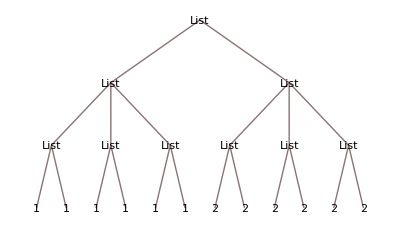

{{1,1,1},{2,2,2}}

0.0027

```mathematica
{{{1,1},{1,1},{1,1}},{{2,2},{2,2},{2,2}}}//TreeForm
Flatten[{{{1},{1},{1}},{{2},{2},{2}}},{{1},{2,3}}]
a=(%//AbsoluteTiming)⟦1⟧*1000
```

```mathematica
Flatten[{{1},{1},{1}},2]
Flatten[#,2]&/@{{{1,1},{1,1},{1,1}},{{2,2},{2,2},{2,2}}}
b=(%//AbsoluteTiming)⟦1⟧*1000
```

{1,1,1}

{{1,1,1,1,1,1},{2,2,2,2,2,2}}

0.0023